# Initialization

```mathematica
Begin["Global`"]
ss[A_]:=Series[(A/.{λ->γ n,nz->n nz,nx->n nx,ny->n ny})//Simplify,{γ,0,3}]//Simplify//Normal
bs[A_]:=Series[(A/.{nz->n nz,nx->n nx,ny->n ny}/.n->η λ)//Simplify,{η,0,3}]//Simplify//Normal
ben[A_]:=Series[A,{ϵ,∞,3}]//Simplify//Normal
ben4[A_]:=Series[A,{ϵ,∞,4}]//Simplify//Normal
ben6[A_]:=Series[A,{ϵ,∞,6}]//Simplify//Normal
subst={px^2->P^2-py^2,px^4->(P^2-py^2)^2,nx^2->n^2-ny^2-nz^2,nx^4->(n^2-ny^2-nz^2)^2};
subst2={nx^pwr_->(n^2-ny^2-nz^2)^Quotient[pwr,2] nx^Mod[pwr,2],mx^pwr_->(m^2-my^2-mz^2)^Quotient[pwr,2] mx^Mod[pwr,2]};
subst2ny={ny^pwr_->(n^2-nx^2-nz^2)^Quotient[pwr,2] ny^Mod[pwr,2],mx^pwr_->(m^2-my^2-mz^2)^Quotient[pwr,2] mx^Mod[pwr,2]};

retarded={ϵ->ϵ(1+ⅈ α),n->n(1-ⅈ α),nx->nx(1-ⅈ α),ny->ny(1-ⅈ α),nz->nz(1-ⅈ α),Λ->Λ(1+ⅈ α)};
advanced={ϵ->ϵ(1-ⅈ α),n->n(1+ⅈ α),nx->nx(1+ⅈ α),ny->ny(1+ⅈ α),nz->nz(1+ⅈ α),Λ->Λ(1-ⅈ α)};

mretarded={m->m(1+ⅈ α),mx->mx(1+ⅈ α),my->my(1+ⅈ α),mz->mz(1+ⅈ α)};
madvanced={m->m(1-ⅈ α),mx->mx(1-ⅈ α),my->my(1-ⅈ α),mz->mz(1-ⅈ α)};

anglesubst={px->P(Exp[I θ]+Exp[-I θ])/2,py->P(Exp[I θ]- Exp[-I θ])/(2 ⅈ)};
anglemean={Power[E,Times[Complex[0,n_],\[Theta]]]->0};
sim={vf->1,J->1};
P2toXWithv=Table[P^k->X^(k/2)/vf^k,{k,2,8,2}];
P2toX=Table[P^k->X^(k/2),{k,2,8,2}];

$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
$Assumptions= {ϵ>0,ϵ^2-n^2>0,λ>0,nx^2<1,ny^2<1,maz^2<1,nz^2<1,n^2>nz^2,{n,nx,ny,nz,λ,Λ,px,py,P,ϵ,m,mx,my,mz,α}∈Reals,{my ny+mz nz+ mx nx ==0,nx^2+ny^2+nz^2==n^2,ndoty ny+ndotx nx+ndotz nz==0}};

Unprotect[NonCommutativeMultiply];
NonCommutativeMultiply[A_?MatrixQ,B_?MatrixQ]:=KroneckerProduct[A,B];
$RecursionLimit=Infinity;
MatrixVectorDot[A_?ListQ,B_?ListQ]:=Sum[A⟦i⟧B⟦i⟧,{i,1,Min[Length[A],Length[B]]}];
MatrixCross[A_?ListQ,B_?ListQ]:={A⟦2⟧**B⟦3⟧-A⟦3⟧**B⟦2⟧,A⟦3⟧**B⟦1⟧-A⟦1⟧**B⟦3⟧,A⟦1⟧**B⟦2⟧-A⟦2⟧**B⟦1⟧};
SetDirectory[NotebookDirectory[]];

σ={σx,σy,σz,σ1}=PauliMatrix[Range[4]];
σK={σx,-σy,σz,σ1};
s={sx,sy,sz,s1}=PauliMatrix[Range[4]];
p={px,py,0};
nv={nx,ny,nz,0};
mv={mx,my,mz,0};
nv1={0,0,0,n};

σRot={(nx σx + ny σy)/(√(nx^2+ny^2)),(ny σx - nx σy)/(√(nx^2+ny^2)),σz,σ1}; 

sel10[A_]:={A[[1,1]],A[[1,2]],A[[1,3]],A[[2,1]],A[[2,2]],A[[2,3]],A[[3,1]],A[[3,2]],A[[3,3]],A[[4,4]]};
sel6[A_]:={A[[1,4]],A[[2,4]],A[[3,4]],A[[4,1]],A[[4,2]],A[[4,3]]};
σsRotUngrouped=Join[Table[σRot[[1]]**σRot[[j]],{j,4}],Table[σRot[[2]]**σRot[[j]],{j,4}],Table[σRot[[3]]**σRot[[j]],{j,4}],Table[σRot[[4]]**σRot[[j]],{j,4}]]//Simplify;
σsRot=Join[Table[σRot[[i]]**σRot[[j]],{i,4},{j,4}]//sel6,Table[σRot[[i]]**σRot[[j]],{i,4},{j,4}]//sel10]//Simplify;

σs=Join[Table[σ[[i]]**σ[[j]],{i,4},{j,4}]//sel6,Table[σ[[i]]**σ[[j]],{i,4},{j,4}]//sel10]//Simplify;

K2[A_]:=ReplaceAll[A,{n->-n,nx->-nx,ny->-ny,nz->-nz,Λ->-Λ}]
Global`Λ0[A_]:=Series[A,{Λ,0,0}]//Normal//Simplify
Global`λ0[A_]:=Series[A,{λ,0,0}]//Normal//Simplify
Global`α0[A_]:=Series[A,{α,0,0}]//Normal//Simplify

Global`Λ2[A_]:=Series[A,{Λ,0,2}]//Normal//Simplify
Global`λ2[A_]:=Series[A,{λ,0,2}]//Normal//Simplify
Global`α2[A_]:=Series[A,{α,0,2}]//Normal//Simplify
Get["Rashba.mx"]
Get["Global.mx"]
```

Global`

```mathematica
up
```

# K1 couplings (assumption doesn’t break the theory because of eigenvalues symmetry)

```mathematica
σRot
```

{{{0,(nx-ⅈ ny)/(√(nx^2+ny^2))},{(nx+ⅈ ny)/(√(nx^2+ny^2)),0}},{{0,(ⅈ nx+ny)/(√(nx^2+ny^2))},{(-ⅈ nx+ny)/(√(nx^2+ny^2)),0}},{{1,0},{0,-1}},{{1,0},{0,1}}}

```mathematica
σRot//K2
```

{{{0,(-nx+ⅈ ny)/(√(nx^2+ny^2))},{(-nx-ⅈ ny)/(√(nx^2+ny^2)),0}},{{0,(-ⅈ nx-ny)/(√(nx^2+ny^2))},{(ⅈ nx-ny)/(√(nx^2+ny^2)),0}},{{1,0},{0,-1}},{{1,0},{0,1}}}

```mathematica
Begin["R`"]
```

R`

## Green functions

```mathematica
R`H=MatrixVectorDot[σ,p]**s1+ σz ** MatrixVectorDot[nv,s]+1/2 λ MatrixCross[σ,s]⟦3⟧;
R`eval=Simplify[Eigenvalues[R`H]]/.subst
R`G=FullSimplify[FullSimplify[Inverse[IdentityMatrix[4]ϵ-R`H]*Det[IdentityMatrix[4]ϵ-R`H]]]/.subst
R`GDet=Det[IdentityMatrix[4]ϵ-R`H]/.subst//FullSimplify;
R`GA=R`G/.advanced;R`GR=R`G/.retarded;
R`res=Simplify[X/.Solve[((R`GDet)/.P2toX)==0,X]/.sim,Assumptions->λ>0]//Simplify
R`resRet1=Series[R`res/.retarded,{α,0,1}]//Normal;
R`resAdv1=Series[R`res/.advanced,{α,0,1}]//Normal;
R`GDet==(P^2-R`res[[1]])(P^2-R`res[[2]])//FullSimplify
```

{1/2 (λ-√(λ^2+4 (n^2+P^2-nz λ))),1/2 (λ+√(λ^2+4 (n^2+P^2-nz λ))),1/2 (-λ-√(λ^2+4 (n^2+P^2+nz λ))),1/2 (-λ+√(λ^2+4 (n^2+P^2+nz λ)))}

(-(nz+ϵ) (n^2+P^2-ϵ^2)+2 (ny px-nx py) λ+(nz-ϵ) λ^2 | -(nx-ⅈ ny) (n^2+P^2-ϵ^2)+(ⅈ px+py) (nz-ϵ) λ | -(px-ⅈ py) (n^2+P^2-ϵ^2)-ⅈ (nx-ⅈ ny) (nz-ϵ) λ | -ⅈ ((nx-ⅈ ny)^2+(px-ⅈ py)^2) λ
-(nx+ⅈ ny) (n^2+P^2-ϵ^2)+(-ⅈ px+py) (nz-ϵ) λ | (nz-ϵ) (n^2+P^2-ϵ^2) | ⅈ (nz-ϵ)^2 λ | -(px-ⅈ py) (n^2+P^2-ϵ^2)+(ⅈ nx+ny) (nz-ϵ) λ
-(px+ⅈ py) (n^2+P^2-ϵ^2)+ⅈ (nx+ⅈ ny) (nz-ϵ) λ | -ⅈ (nz-ϵ)^2 λ | (nz-ϵ) (n^2+P^2-ϵ^2) | (nx-ⅈ ny) (n^2+P^2-ϵ^2)+(ⅈ px+py) (nz-ϵ) λ
ⅈ ((nx+ⅈ ny)^2+(px+ⅈ py)^2) λ | -(px+ⅈ py) (n^2+P^2-ϵ^2)+(-ⅈ nx+ny) (nz-ϵ) λ | (nx+ⅈ ny) (n^2+P^2-ϵ^2)+(-ⅈ px+py) (nz-ϵ) λ | -(nz+ϵ) (n^2+P^2-ϵ^2)+2 (-ny px+nx py) λ+(nz-ϵ) λ^2)

{-n^2+ϵ^2+nz λ-ϵ λ,-n^2+ϵ^2-nz λ+ϵ λ}

```mathematica
R`resRet1
```

{-n^2+ϵ^2+nz λ-ϵ λ+ⅈ α (2 n^2+2 ϵ^2-nz λ-ϵ λ),-n^2+ϵ^2-nz λ+ϵ λ+ⅈ α (2 n^2+2 ϵ^2+nz λ+ϵ λ)}

```mathematica
R`resR=R`res/.retarded;
R`resA=R`res/.advanced;
```

```mathematica
R`evalF[ω_,λ_,n_,nz_,P_]={R`eval/.nz->n nz,(λ+n)/ω}//Flatten
```

{1/2 (λ-√(λ^2+4 (n^2+P^2-n nz λ))),1/2 (λ+√(λ^2+4 (n^2+P^2-n nz λ))),1/2 (-λ-√(λ^2+4 (n^2+P^2+n nz λ))),1/2 (-λ+√(λ^2+4 (n^2+P^2+n nz λ))),(n+λ)/ω}

```mathematica
(*R`evec=Eigenvectors[R`H]/.subst//Simplify*)
```

```mathematica
R`evec
```

(-ⅈ nx-ny-px+ⅈ py | ⅈ nz-(ⅈ λ)/2+1/2 ⅈ √(4 n^2+4 P^2-4 nz λ+λ^2) | nz-λ/2+1/2 √(4 n^2+4 P^2-4 nz λ+λ^2) | nx+ⅈ ny-ⅈ px+py
-ⅈ nx-ny-px+ⅈ py | ⅈ nz-(ⅈ λ)/2-1/2 ⅈ √(4 n^2+4 P^2-4 nz λ+λ^2) | nz-λ/2-1/2 √(4 n^2+4 P^2-4 nz λ+λ^2) | nx+ⅈ ny-ⅈ px+py
ⅈ nx+ny-px+ⅈ py | -ⅈ nz-(ⅈ λ)/2-1/2 ⅈ √(4 n^2+4 P^2+4 nz λ+λ^2) | nz+λ/2+1/2 √(4 n^2+4 P^2+4 nz λ+λ^2) | nx+ⅈ ny+ⅈ px-py
ⅈ nx+ny-px+ⅈ py | -ⅈ nz-(ⅈ λ)/2+1/2 ⅈ √(4 n^2+4 P^2+4 nz λ+λ^2) | nz+λ/2-1/2 √(4 n^2+4 P^2+4 nz λ+λ^2) | nx+ⅈ ny+ⅈ px-py)

```mathematica
R`evecconjtr.R`evec//Simplify
```

(4 (nx^2+ny^2+px^2+py^2) | -2 (2 nx nz+2 ⅈ ny nz+(-ⅈ px+py) λ) | -4 nz (px+ⅈ py)+2 (-ⅈ nx+ny) λ | 0
-4 nx nz+4 ⅈ ny nz-2 (ⅈ px+py) λ | 2 (2 n^2+2 nz^2+2 P^2+λ^2) | 8 ⅈ nz λ | -2 (2 nz (px+ⅈ py)+(-ⅈ nx+ny) λ)
-4 nz px+4 ⅈ nz py+2 ⅈ nx λ+2 ny λ | -8 ⅈ nz λ | 2 (2 n^2+2 nz^2+2 P^2+λ^2) | 4 nx nz+4 ⅈ ny nz+2 ⅈ px λ-2 py λ
0 | -2 (2 nz (px-ⅈ py)+(ⅈ nx+ny) λ) | 4 nx nz-4 ⅈ ny nz-2 ⅈ px λ-2 py λ | 4 (nx^2+ny^2+px^2+py^2))

```mathematica
R`evecconjtr=R`evec//Expand//ConjugateTranspose//Simplify;
```

```mathematica
R`evmod=R`evec.R`evecconjtr//Simplify//#/.subst&//Simplify
```

(4 n^2+4 P^2-4 nz λ+λ^2+2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)-λ √(4 n^2+4 P^2-4 nz λ+λ^2) | 0 | 0 | 0
0 | 4 n^2+4 P^2-4 nz λ+λ^2-2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)+λ √(4 n^2+4 P^2-4 nz λ+λ^2) | 0 | 0
0 | 0 | 4 n^2+4 P^2+4 nz λ+λ^2+2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)+λ √(4 n^2+4 P^2+4 nz λ+λ^2) | 0
0 | 0 | 0 | 4 n^2+4 P^2+4 nz λ+λ^2-2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)-λ √(4 n^2+4 P^2+4 nz λ+λ^2))

```mathematica
R`evecNorm={(R`evec[[1]])/(√(R`evmod[[1,1]])),(R`evec[[2]])/(√(R`evmod[[2,2]])),(R`evec[[3]])/(√(R`evmod[[3,3]])),(R`evec[[4]])/(√(R`evmod[[4,4]]))}
```

((-ⅈ nx-ny-px+ⅈ py)/(√(4 n^2+4 P^2-4 nz λ+λ^2+2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)-λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (ⅈ nz-(ⅈ λ)/2+1/2 ⅈ √(4 n^2+4 P^2-4 nz λ+λ^2))/(√(4 n^2+4 P^2-4 nz λ+λ^2+2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)-λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (nz-λ/2+1/2 √(4 n^2+4 P^2-4 nz λ+λ^2))/(√(4 n^2+4 P^2-4 nz λ+λ^2+2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)-λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (nx+ⅈ ny-ⅈ px+py)/(√(4 n^2+4 P^2-4 nz λ+λ^2+2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)-λ √(4 n^2+4 P^2-4 nz λ+λ^2)))
(-ⅈ nx-ny-px+ⅈ py)/(√(4 n^2+4 P^2-4 nz λ+λ^2-2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)+λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (ⅈ nz-(ⅈ λ)/2-1/2 ⅈ √(4 n^2+4 P^2-4 nz λ+λ^2))/(√(4 n^2+4 P^2-4 nz λ+λ^2-2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)+λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (nz-λ/2-1/2 √(4 n^2+4 P^2-4 nz λ+λ^2))/(√(4 n^2+4 P^2-4 nz λ+λ^2-2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)+λ √(4 n^2+4 P^2-4 nz λ+λ^2))) | (nx+ⅈ ny-ⅈ px+py)/(√(4 n^2+4 P^2-4 nz λ+λ^2-2 nz √(4 n^2+4 P^2-4 nz λ+λ^2)+λ √(4 n^2+4 P^2-4 nz λ+λ^2)))
(ⅈ nx+ny-px+ⅈ py)/(√(4 n^2+4 P^2+4 nz λ+λ^2+2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)+λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (-ⅈ nz-(ⅈ λ)/2-1/2 ⅈ √(4 n^2+4 P^2+4 nz λ+λ^2))/(√(4 n^2+4 P^2+4 nz λ+λ^2+2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)+λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (nz+λ/2+1/2 √(4 n^2+4 P^2+4 nz λ+λ^2))/(√(4 n^2+4 P^2+4 nz λ+λ^2+2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)+λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (nx+ⅈ ny+ⅈ px-py)/(√(4 n^2+4 P^2+4 nz λ+λ^2+2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)+λ √(4 n^2+4 P^2+4 nz λ+λ^2)))
(ⅈ nx+ny-px+ⅈ py)/(√(4 n^2+4 P^2+4 nz λ+λ^2-2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)-λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (-ⅈ nz-(ⅈ λ)/2+1/2 ⅈ √(4 n^2+4 P^2+4 nz λ+λ^2))/(√(4 n^2+4 P^2+4 nz λ+λ^2-2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)-λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (nz+λ/2-1/2 √(4 n^2+4 P^2+4 nz λ+λ^2))/(√(4 n^2+4 P^2+4 nz λ+λ^2-2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)-λ √(4 n^2+4 P^2+4 nz λ+λ^2))) | (nx+ⅈ ny+ⅈ px-py)/(√(4 n^2+4 P^2+4 nz λ+λ^2-2 nz √(4 n^2+4 P^2+4 nz λ+λ^2)-λ √(4 n^2+4 P^2+4 nz λ+λ^2))))

{-ⅈ nx-ny-px+ⅈ py,ⅈ nz-(ⅈ λ)/2+1/2 ⅈ √(4 n^2+4 P^2-4 nz λ+λ^2),nz-λ/2+1/2 √(4 n^2+4 P^2-4 nz λ+λ^2),nx+ⅈ ny-ⅈ px+py}

```mathematica
R`evecconjtr.σ1**σz.R`evec//Simplify//#/.subst&//Simplify
```

(0 | (-ⅈ px+py) (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))-nx (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))-ⅈ ny (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | 1/2 (2 ⅈ nx √(4 n^2+4 P^2+λ (-4 nz+λ))-2 (ny+px+ⅈ py) √(4 n^2+4 P^2+λ (-4 nz+λ))+(ⅈ nx-ny+px+ⅈ py) (2 nz+λ-√(4 n^2+4 P^2+4 nz λ+λ^2))+(-ⅈ nx+ny-px-ⅈ py) (2 nz+λ+√(4 n^2+4 P^2+4 nz λ+λ^2))) | 0
(ⅈ px+py) (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))-nx (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))+ⅈ ny (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | λ (-√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))+2 nz (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -2 ⅈ nz (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))+ⅈ λ (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -1/2 ⅈ (-2 nx √(4 n^2+4 P^2+λ (4 nz+λ))-2 ⅈ (ny+px+ⅈ py) √(4 n^2+4 P^2+λ (4 nz+λ))+(nx+ⅈ ny-ⅈ px+py) (2 nz-λ+√(4 n^2+4 P^2-4 nz λ+λ^2))+(nx+ⅈ ny-ⅈ px+py) (-2 nz+λ+√(4 n^2+4 P^2-4 nz λ+λ^2)))
-ⅈ nx (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))+ny (-√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))-(px-ⅈ py) (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -ⅈ (-2 nz (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))+λ (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))) | λ (-√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))+2 nz (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | 1/2 (2 nx √(4 n^2+4 P^2+λ (4 nz+λ))+2 ⅈ (ny+px+ⅈ py) √(4 n^2+4 P^2+λ (4 nz+λ))+(nx+ⅈ ny-ⅈ px+py) (2 nz-λ+√(4 n^2+4 P^2-4 nz λ+λ^2))+(nx+ⅈ ny-ⅈ px+py) (-2 nz+λ+√(4 n^2+4 P^2-4 nz λ+λ^2)))
0 | ⅈ nx (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))+ny (√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))-(px-ⅈ py) (√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | 1/2 (2 nx √(4 n^2+4 P^2+λ (4 nz+λ))-2 ⅈ (ny+px-ⅈ py) √(4 n^2+4 P^2+λ (4 nz+λ))+(nx-ⅈ ny+ⅈ px+py) (2 nz-λ+√(4 n^2+4 P^2-4 nz λ+λ^2))+(nx-ⅈ ny+ⅈ px+py) (-2 nz+λ+√(4 n^2+4 P^2-4 nz λ+λ^2))) | 0)

```mathematica
%/.nz->0/.n->0
```

(0 | -2 nx √(4 P^2+λ^2)-2 ⅈ ny √(4 P^2+λ^2) | 1/2 (2 ⅈ nx √(4 P^2+λ^2)-2 (ny+px+ⅈ py) √(4 P^2+λ^2)+(ⅈ nx-ny+px+ⅈ py) (λ-√(4 P^2+λ^2))+(-ⅈ nx+ny-px-ⅈ py) (λ+√(4 P^2+λ^2))) | 0
-2 nx √(4 P^2+λ^2)+2 ⅈ ny √(4 P^2+λ^2) | 0 | 2 ⅈ λ √(4 P^2+λ^2) | -1/2 ⅈ (-2 nx √(4 P^2+λ^2)-2 ⅈ (ny+px+ⅈ py) √(4 P^2+λ^2)+(nx+ⅈ ny-ⅈ px+py) (-λ+√(4 P^2+λ^2))+(nx+ⅈ ny-ⅈ px+py) (λ+√(4 P^2+λ^2)))
-2 (px-ⅈ py) √(4 P^2+λ^2) | -2 ⅈ λ √(4 P^2+λ^2) | 0 | 1/2 (2 nx √(4 P^2+λ^2)+2 ⅈ (ny+px+ⅈ py) √(4 P^2+λ^2)+(nx+ⅈ ny-ⅈ px+py) (-λ+√(4 P^2+λ^2))+(nx+ⅈ ny-ⅈ px+py) (λ+√(4 P^2+λ^2)))
0 | -2 (px-ⅈ py) √(4 P^2+λ^2) | 1/2 (2 nx √(4 P^2+λ^2)-2 ⅈ (ny+px-ⅈ py) √(4 P^2+λ^2)+(nx-ⅈ ny+ⅈ px+py) (-λ+√(4 P^2+λ^2))+(nx-ⅈ ny+ⅈ px+py) (λ+√(4 P^2+λ^2))) | 0)

```mathematica
R`evec.σ1**σx.R`evecconjtr//Simplify//#/.subst&//Simplify
```

(2 py (2 nz-λ+√(4 n^2+4 P^2-4 nz λ+λ^2)) | 4 nz py-2 py λ-2 ⅈ ny √(4 n^2+4 P^2+λ (-4 nz+λ)) | (nx-ⅈ px) (4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | (nx-ⅈ px) (4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2))
4 nz py-2 py λ+2 ⅈ ny √(4 n^2+4 P^2-4 nz λ+λ^2) | -2 py (-2 nz+λ+√(4 n^2+4 P^2-4 nz λ+λ^2)) | -(nx-ⅈ px) (-4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2)) | -(nx-ⅈ px) (-4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2))
(nx+ⅈ px) (4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -(nx+ⅈ px) (-4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2)) | -2 py (2 nz+λ+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -2 (2 nz py+py λ+ⅈ ny √(4 n^2+4 P^2+4 nz λ+λ^2))
(nx+ⅈ px) (4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)-√(4 n^2+4 P^2+4 nz λ+λ^2)) | -(nx+ⅈ px) (-4 nz+√(4 n^2+4 P^2-4 nz λ+λ^2)+√(4 n^2+4 P^2+4 nz λ+λ^2)) | -4 nz py-2 py λ+2 ⅈ ny √(4 n^2+4 P^2+4 nz λ+λ^2) | 2 py (-2 nz-λ+√(4 n^2+4 P^2+4 nz λ+λ^2)))

```mathematica
Eigenvectors[R`H]/.subst/.nz->n//Simplify
```

(-(ⅈ nx+ny+px-ⅈ py)/(nx+ⅈ ny-ⅈ px+py) | (ⅈ (2 n-λ+√(4 n^2+4 P^2-4 n λ+λ^2)))/(2 (nx+ⅈ ny-ⅈ px+py)) | (2 n-λ+√(4 n^2+4 P^2-4 n λ+λ^2))/(2 (nx+ⅈ ny-ⅈ px+py)) | 1
-(ⅈ nx+ny+px-ⅈ py)/(nx+ⅈ ny-ⅈ px+py) | -(ⅈ (-2 n+λ+√(4 n^2+4 P^2-4 n λ+λ^2)))/(2 (nx+ⅈ ny-ⅈ px+py)) | -(-2 n+λ+√(4 n^2+4 P^2-4 n λ+λ^2))/(2 (nx+ⅈ ny-ⅈ px+py)) | 1
(ⅈ nx+ny-px+ⅈ py)/(nx+ⅈ (ny+px+ⅈ py)) | -(ⅈ (2 n+λ+√(4 n^2+4 P^2+4 n λ+λ^2)))/(2 (nx+ⅈ (ny+px+ⅈ py))) | (2 n+λ+√(4 n^2+4 P^2+4 n λ+λ^2))/(2 (nx+ⅈ (ny+px+ⅈ py))) | 1
(ⅈ nx+ny-px+ⅈ py)/(nx+ⅈ (ny+px+ⅈ py)) | (ⅈ (-2 n-λ+√(4 n^2+4 P^2+4 n λ+λ^2)))/(2 (nx+ⅈ (ny+px+ⅈ py))) | (2 n+λ-√(4 n^2+4 P^2+4 n λ+λ^2))/(2 (nx+ⅈ (ny+px+ⅈ py))) | 1)

## Leading order

```mathematica
R`bubble00[k_]:=R`bubble00[k]=Module[{bubble},
bubble=ⅈ α(X^k/((X-R`resAdv1[[1]])(X-R`resAdv1[[2]])(X-R`resRet1[[1]])(X-R`resRet1[[2]])))/.subst//Simplify;
Residue[bubble,{X,R`resRet1[[1]]}]+ Residue[bubble,{X,R`resRet1[[2]]}]//Series[#,{α,0,0}]&//Normal];
R`integrateList0=Table[R`bubble00[k]//Simplify,{k,0,5}];
R`tr0[A_,B_]:=R`tr0[A,B]=1/2((Tr[A.R`G.B.R`G]/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
```

```mathematica
R`coupling[A_,B_]:=R`coupling[A,B]=Table[R`tr0[A⟦i⟧,B⟦j⟧].R`integrateList0//Simplify,{i,1,16},{j,1,16}];
```

```mathematica
R`couplingRot=(R`coupling[σsRot,σsRot]/.subst2//Simplify)/.(n^2-2 ⅈ nx ny-2 ny^2-nz^2)->(nx-ⅈ ny)^2 //Simplify;
```

```mathematica
R`couplingUnRot=(R`coupling[σs,σs]/.subst2//Simplify)/.(n^2-2 ⅈ nx ny-2 ny^2-nz^2)->(nx-ⅈ ny)^2 //Simplify;
```

```mathematica
R`couplingABRot=(R`coupling[σABsRot,σABsRot]/.subst2//Simplify)/.(n^2-2 ⅈ nx ny-2 ny^2-nz^2)->(nx-ⅈ ny)^2 //Simplify;
```

```mathematica
(IdentityMatrix[16]-R`couplingABRot)//NullSpace
```

{}

```mathematica
R`couplingRot.R`nullVectorᵀ//Simplify
```

(0
0
0
0
0
0
0
0
0
0
0
0
(√(n^2-nz^2))/ϵ
0
nz/ϵ
1)

```mathematica
(-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))//ben
```

1/2+(nz λ^2)/(4 ϵ^3)+(-n^2-λ^2/8)/ϵ^2

```mathematica
(R`couplingRot//Simplify)//Simplify
```

((-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | -((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (√(n^2-nz^2) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√(n^2-nz^2) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (√(n^2-nz^2) (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√(n^2-nz^2) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-n^6+n^4 ϵ^2+n^2 ϵ (ϵ^3+2 nz λ^2-2 ϵ λ^2)-ϵ^2 (ϵ^4+2 nz^2 λ^2-2 nz ϵ λ^2))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | (n^6-n^4 ϵ^2-n^2 ϵ (ϵ^3+2 nz λ^2-2 ϵ λ^2)+ϵ^2 (ϵ^4+2 nz^2 λ^2-2 nz ϵ λ^2))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3 n^6+n^4 (8 nz-5 ϵ) ϵ+ϵ^2 (-3 ϵ^4-2 nz^2 (4 ϵ^2+λ^2)+2 nz ϵ (4 ϵ^2+λ^2))+n^2 ϵ (-8 nz^2 ϵ-5 ϵ^3-2 ϵ λ^2+2 nz (8 ϵ^2+λ^2)))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (-3 n^6+n^4 (4 nz^2-ϵ^2)+n^2 ϵ (-8 nz^3+16 nz^2 ϵ-8 nz ϵ^2+3 ϵ^3+2 nz λ^2-2 ϵ λ^2)+ϵ^2 (-8 nz^3 ϵ+ϵ^4+2 nz^2 (6 ϵ^2-λ^2)+nz (-8 ϵ^3+2 ϵ λ^2)))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2+ϵ^2) (n^2+ϵ (-2 nz+ϵ)))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | -(√(n^2-nz^2) (nz+ϵ) (n^2+ϵ (-2 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^4-n^2 (nz^2+3 nz ϵ-2 ϵ^2)+ϵ (2 nz^3+nz^2 ϵ-3 nz ϵ^2+ϵ^3)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((n^4+nz (2 nz-ϵ) ϵ^2+n^2 ϵ (-3 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-3 n^6+n^4 (4 nz^2-ϵ^2)+n^2 ϵ (-8 nz^3+16 nz^2 ϵ-8 nz ϵ^2+3 ϵ^3+2 nz λ^2-2 ϵ λ^2)+ϵ^2 (-8 nz^3 ϵ+ϵ^4+2 nz^2 (6 ϵ^2-λ^2)+nz (-8 ϵ^3+2 ϵ λ^2)))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (-3 n^6+n^4 (8 nz^2-8 nz ϵ+3 ϵ^2)+n^2 (-8 nz^4+16 nz^3 ϵ-8 nz^2 ϵ^2+3 ϵ^4+2 nz ϵ λ^2-2 ϵ^2 λ^2)+ϵ^2 (-8 nz^4+16 nz^3 ϵ-3 ϵ^4+2 nz ϵ (4 ϵ^2+λ^2)-2 nz^2 (8 ϵ^2+λ^2)))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2-2 nz^2+2 nz ϵ-ϵ^2) (n^2+ϵ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | -(√(n^2-nz^2) (nz+ϵ) (n^2-2 nz^2+2 nz ϵ-ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^4+2 nz^4-3 nz^2 ϵ^2+3 nz ϵ^3-ϵ^4+n^2 nz (-3 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((n^4+nz ϵ (2 nz^2-2 nz ϵ+ϵ^2)-n^2 (2 nz^2-nz ϵ+ϵ^2)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))
0 | 0 | 0 | 0 | 0 | 0 | (n^6-n^4 ϵ^2-n^2 ϵ (ϵ^3+2 nz λ^2-2 ϵ λ^2)+ϵ^2 (ϵ^4+2 nz^2 λ^2-2 nz ϵ λ^2))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | -(n^6-n^4 ϵ^2-n^2 ϵ (ϵ^3+2 nz λ^2-2 ϵ λ^2)+ϵ^2 (ϵ^4+2 nz^2 λ^2-2 nz ϵ λ^2))/(2 (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 √(n^2-nz^2) (n^2+ϵ^2) (n^2+ϵ (-2 nz+ϵ)))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2-2 nz^2+2 nz ϵ-ϵ^2) (n^2+ϵ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (4 (n^2-nz^2) (n^2+ϵ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (2 (n^2-nz^2) (nz+ϵ) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2-nz^2-nz ϵ+ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | -(2 √(n^2-nz^2) (n^2-nz ϵ) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(n^2-nz^2) (nz+ϵ) (n^2+ϵ (-2 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(√(n^2-nz^2) (nz+ϵ) (n^2-2 nz^2+2 nz ϵ-ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (2 (n^2-nz^2) (nz+ϵ) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (4 (n^2-nz^2) (n^2+ϵ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (√(n^2-nz^2) (4 n^2 nz+4 nz ϵ^2-nz λ^2-ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (4 n^2 ϵ+4 ϵ^3-nz λ^2-ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((n^4-n^2 (nz^2+3 nz ϵ-2 ϵ^2)+ϵ (2 nz^3+nz^2 ϵ-3 nz ϵ^2+ϵ^3)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^4+2 nz^4-3 nz^2 ϵ^2+3 nz ϵ^3-ϵ^4+n^2 nz (-3 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2-nz^2-nz ϵ+ϵ^2) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (4 n^2 nz+4 nz ϵ^2-nz λ^2-ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (-2 nz ϵ λ^2+ϵ^2 λ^2+nz^2 (4 ϵ^2-2 λ^2)+n^2 (4 nz^2+λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (n^2 (4 nz ϵ+λ^2)-nz (-4 ϵ^3+nz λ^2+2 ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((n^4+nz (2 nz-ϵ) ϵ^2+n^2 ϵ (-3 nz+ϵ)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | ((n^4+nz ϵ (2 nz^2-2 nz ϵ+ϵ^2)-n^2 (2 nz^2-nz ϵ+ϵ^2)) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | -(2 √(n^2-nz^2) (n^2-nz ϵ) λ)/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (√(n^2-nz^2) (4 n^2 ϵ+4 ϵ^3-nz λ^2-ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | 0 | (n^2 (4 nz ϵ+λ^2)-nz (-4 ϵ^3+nz λ^2+2 ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (n^2 (4 ϵ^2+λ^2)+ϵ (4 ϵ^3-2 nz λ^2-ϵ λ^2))/((2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)))

## Dressings, projector to subspace (coupling to this subspace is zero?).

```mathematica
R`G
```

(-(nz+ϵ) (n^2+P^2-ϵ^2)+2 (ny px-nx py) λ+(nz-ϵ) λ^2 | -(nx-ⅈ ny) (n^2+P^2-ϵ^2)+(ⅈ px+py) (nz-ϵ) λ | -(px-ⅈ py) (n^2+P^2-ϵ^2)-ⅈ (nx-ⅈ ny) (nz-ϵ) λ | -ⅈ ((nx-ⅈ ny)^2+(px-ⅈ py)^2) λ
-(nx+ⅈ ny) (n^2+P^2-ϵ^2)+(-ⅈ px+py) (nz-ϵ) λ | (nz-ϵ) (n^2+P^2-ϵ^2) | ⅈ (nz-ϵ)^2 λ | -(px-ⅈ py) (n^2+P^2-ϵ^2)+(ⅈ nx+ny) (nz-ϵ) λ
-(px+ⅈ py) (n^2+P^2-ϵ^2)+ⅈ (nx+ⅈ ny) (nz-ϵ) λ | -ⅈ (nz-ϵ)^2 λ | (nz-ϵ) (n^2+P^2-ϵ^2) | (nx-ⅈ ny) (n^2+P^2-ϵ^2)+(ⅈ px+py) (nz-ϵ) λ
ⅈ ((nx+ⅈ ny)^2+(px+ⅈ py)^2) λ | -(px+ⅈ py) (n^2+P^2-ϵ^2)+(-ⅈ nx+ny) (nz-ϵ) λ | (nx+ⅈ ny) (n^2+P^2-ϵ^2)+(-ⅈ px+py) (nz-ϵ) λ | -(nz+ϵ) (n^2+P^2-ϵ^2)+2 (-ny px+nx py) λ+(nz-ϵ) λ^2)

```mathematica
R`tr0[R`σDivNorm,R`σDivNorm].R`integrateList0//Simplify
```

1/4

```mathematica
R`σDivNorm=(R`σDiv)/(√((4 (n^2+ϵ^2))/ϵ^2))//Simplify
```

(ϵ R`σDiv)/(2 √(n^2+ϵ^2))

```mathematica
Tr[R`σDiv.R`σDiv]//Simplify
```

(4 (nx^2+ny^2+nz^2+ϵ^2))/ϵ^2

```mathematica
R`nullVector=NullSpace[IdentityMatrix[16]-R`couplingRot]//Simplify
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(n^2-nz^2))/ϵ | 0 | nz/ϵ | 1)

```mathematica
R`projectorToN=(R`nullVectorᵀ.R`nullVector)/(R`nullVector//Norm)^2//Simplify
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (n^2-nz^2)/(n^2+ϵ^2) | 0 | (nz √(n^2-nz^2))/(n^2+ϵ^2) | (√(n^2-nz^2) ϵ)/(n^2+ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (nz √(n^2-nz^2))/(n^2+ϵ^2) | 0 | nz^2/(n^2+ϵ^2) | (nz ϵ)/(n^2+ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(n^2-nz^2) ϵ)/(n^2+ϵ^2) | 0 | (nz ϵ)/(n^2+ϵ^2) | ϵ^2/(n^2+ϵ^2))

```mathematica
Tr[R`projectorToN]//Simplify
```

1

```mathematica
R`projectorToN.R`projectorToN==R`projectorToN//Simplify
```

True

```mathematica
R`couplingRotProj=(IdentityMatrix[16]-R`projectorToN).R`couplingRot.(IdentityMatrix[16]-R`projectorToN)//Simplify;
```

```mathematica
R`couplingRotProj//ben
```

(1/2+(nz λ^2)/(4 ϵ^3)+(-n^2-λ^2/8)/ϵ^2 | 0 | 0 | 0 | -(3 nz λ)/(4 ϵ^2)+λ/(4 ϵ)+(4 n^2 λ+λ^3)/(16 ϵ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2+(nz λ^2)/(4 ϵ^3)+(-n^2-λ^2/8)/ϵ^2 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(4 ϵ^2) | (3 nz λ)/(4 ϵ^2)-λ/(4 ϵ)-(λ (4 n^2+λ^2))/(16 ϵ^3) | 0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(4 ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(4 ϵ^2) | (nz (n^2-nz^2))/ϵ^3+(n^2-nz^2)/(2 ϵ^2) | (nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)-(√(n^2-nz^2) (8 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | (nz (n^2-nz^2))/ϵ^3+(n^2-nz^2)/(2 ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 nz λ)/(4 ϵ^2)-λ/(4 ϵ)-(λ (4 n^2+λ^2))/(16 ϵ^3) | (nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)-(√(n^2-nz^2) (8 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 1/2+(nz λ^2)/(4 ϵ^3)+(-n^2-λ^2/8)/ϵ^2 | 0 | (nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)-(√(n^2-nz^2) (8 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(3 nz λ)/(4 ϵ^2)+λ/(4 ϵ)+(4 n^2 λ+λ^3)/(16 ϵ^3) | 0 | 0 | 0 | 1/2+(nz λ^2)/(4 ϵ^3)+(-n^2-λ^2/8)/ϵ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(4 ϵ^2) | (nz (n^2-nz^2))/ϵ^3+(n^2-nz^2)/(2 ϵ^2) | (nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)-(√(n^2-nz^2) (8 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | (nz (n^2-nz^2))/ϵ^3+(n^2-nz^2)/(2 ϵ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/8+nz/(4 ϵ)-(nz (6 n^2-4 nz^2+λ^2))/(8 ϵ^3)+(-12 n^2+12 nz^2+λ^2)/(32 ϵ^2) | 0 | 0 | 0 | -1/8-nz/(4 ϵ)+(12 n^2-12 nz^2-λ^2)/(32 ϵ^2)+(nz (6 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/8-nz/(4 ϵ)-(nz (2 n^2-4 nz^2+λ^2))/(8 ϵ^3)+(-4 n^2+4 nz^2+3 λ^2)/(32 ϵ^2) | 0 | -1/8+(3 nz)/(4 ϵ)+(-4 n^2+4 nz^2-λ^2)/(32 ϵ^2)-(nz (10 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | (nz √(n^2-nz^2))/(2 ϵ^2)-(√(n^2-nz^2))/(2 ϵ)+(√(n^2-nz^2) (4 nz^2-λ^2))/(8 ϵ^3) | -(√(n^2-nz^2) λ)/(4 ϵ^2) | 0 | -(nz λ)/(2 ϵ^2)+λ/(4 ϵ)+(-4 nz^2 λ+λ^3)/(16 ϵ^3) | ((n^2+nz^2) λ)/(4 ϵ^3)-(nz λ)/(4 ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8+(3 nz)/(4 ϵ)+(-4 n^2+4 nz^2-λ^2)/(32 ϵ^2)-(nz (10 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | 3/8-nz/(4 ϵ)-(nz (2 n^2-4 nz^2+λ^2))/(8 ϵ^3)+(3 (-12 n^2+12 nz^2+λ^2))/(32 ϵ^2) | 0 | -(nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)+(√(n^2-nz^2) (-8 n^2+4 nz^2+λ^2))/(8 ϵ^3) | (√(n^2-nz^2) λ)/(4 ϵ^2) | 0 | (nz λ)/(2 ϵ^2)-λ/(4 ϵ)-(λ (-8 n^2+4 nz^2+λ^2))/(16 ϵ^3) | -((n^2+nz^2) λ)/(4 ϵ^3)+(nz λ)/(4 ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | -1/8-nz/(4 ϵ)+(12 n^2-12 nz^2-λ^2)/(32 ϵ^2)+(nz (6 n^2-4 nz^2+λ^2))/(8 ϵ^3) | 0 | 0 | 0 | 1/8+nz/(4 ϵ)-(nz (6 n^2-4 nz^2+λ^2))/(8 ϵ^3)+(-12 n^2+12 nz^2+λ^2)/(32 ϵ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (nz √(n^2-nz^2))/(2 ϵ^2)-(√(n^2-nz^2))/(2 ϵ)+(√(n^2-nz^2) (4 nz^2-λ^2))/(8 ϵ^3) | 0 | -(nz √(n^2-nz^2))/(2 ϵ^2)+(√(n^2-nz^2))/(2 ϵ)+(√(n^2-nz^2) (-8 n^2+4 nz^2+λ^2))/(8 ϵ^3) | 0 | (n^2-nz^2)/ϵ^2 | ((n^2-nz^2) λ)/(2 ϵ^3) | 0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(2 ϵ^2) | (nz √(n^2-nz^2) λ)/(2 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(n^2-nz^2) λ)/(4 ϵ^2) | 0 | (√(n^2-nz^2) λ)/(4 ϵ^2) | 0 | ((n^2-nz^2) λ)/(2 ϵ^3) | 0 | 0 | -(√(n^2-nz^2) λ^2)/(4 ϵ^3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(nz λ)/(2 ϵ^2)+λ/(4 ϵ)+(-4 nz^2 λ+λ^3)/(16 ϵ^3) | 0 | (nz λ)/(2 ϵ^2)-λ/(4 ϵ)-(λ (-8 n^2+4 nz^2+λ^2))/(16 ϵ^3) | 0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3)-(√(n^2-nz^2) λ)/(2 ϵ^2) | -(√(n^2-nz^2) λ^2)/(4 ϵ^3) | 0 | -(nz λ^2)/(2 ϵ^3)+λ^2/(4 ϵ^2) | -(nz λ^2)/(4 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((n^2+nz^2) λ)/(4 ϵ^3)-(nz λ)/(4 ϵ^2) | 0 | -((n^2+nz^2) λ)/(4 ϵ^3)+(nz λ)/(4 ϵ^2) | 0 | (nz √(n^2-nz^2) λ)/(2 ϵ^3) | 0 | 0 | -(nz λ^2)/(4 ϵ^3) | 0)

```mathematica
R`couplingRotInversed=Inverse[IdentityMatrix[16]-R`couplingRotProj]//Simplify;
```

```mathematica
R`couplingRotInversed//ben//Simplify
```

(2-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | 0 | 0 | 0 | ((-3 n^2+ϵ (-3 nz+ϵ)) λ)/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | (√(n^2-nz^2) (2 nz-ϵ) λ)/ϵ^3 | ((n^2+2 nz^2+3 nz ϵ-ϵ^2) λ)/ϵ^3 | 0 | (√(n^2-nz^2) (2 nz-ϵ) λ)/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√(n^2-nz^2) (2 nz-ϵ) λ)/ϵ^3 | (-2 nz^3-nz^2 ϵ+ϵ^3+n^2 (2 nz+ϵ))/ϵ^3 | (√(n^2-nz^2) (-2 n^2-nz^2+nz ϵ+ϵ^2))/ϵ^3 | 0 | ((n^2-nz^2) (2 nz+ϵ))/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((n^2+2 nz^2+3 nz ϵ-ϵ^2) λ)/ϵ^3 | (√(n^2-nz^2) (-2 n^2-nz^2+nz ϵ+ϵ^2))/ϵ^3 | -(2 (2 nz^3+nz^2 ϵ-ϵ^3+n^2 (-2 nz+ϵ)+nz λ^2))/ϵ^3 | 0 | (√(n^2-nz^2) (-2 n^2-nz^2+nz ϵ+ϵ^2))/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-3 n^2+ϵ (-3 nz+ϵ)) λ)/ϵ^3 | 0 | 0 | 0 | 2-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (√(n^2-nz^2) (2 nz-ϵ) λ)/ϵ^3 | ((n^2-nz^2) (2 nz+ϵ))/ϵ^3 | (√(n^2-nz^2) (-2 n^2-nz^2+nz ϵ+ϵ^2))/ϵ^3 | 0 | (-2 nz^3-nz^2 ϵ+ϵ^3+n^2 (2 nz+ϵ))/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (320 nz^3+156 nz^2 ϵ+72 nz ϵ^2+189 ϵ^3-36 n^2 (10 nz+3 ϵ)-24 nz λ^2+9 ϵ λ^2)/(162 ϵ^3) | 0 | 0 | 0 | (-320 nz^3-156 nz^2 ϵ+36 n^2 (10 nz+3 ϵ)+24 nz (-3 ϵ^2+λ^2)-9 ϵ (3 ϵ^2+λ^2))/(162 ϵ^3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-182 nz^3-54 n^2 (6 nz-ϵ)+294 nz^2 ϵ+45 ϵ (3 ϵ^2+λ^2)-3 nz (42 ϵ^2+85 λ^2))/(81 ϵ^3) | 0 | (646 nz^3-246 nz^2 ϵ-18 n^2 (10 nz+3 ϵ)+33 nz (6 ϵ^2+7 λ^2)-9 (3 ϵ^3+4 ϵ λ^2))/(81 ϵ^3) | 0 | -(√(n^2-nz^2) (4 n^2+11 nz^2-9 nz ϵ+3 (ϵ^2+λ^2)))/(3 ϵ^3) | (√(n^2-nz^2) (2 nz-ϵ) λ)/(2 ϵ^3) | 0 | (λ (4 n^2+17 nz^2-12 nz ϵ+3 (ϵ^2+λ^2)))/(6 ϵ^3) | ((n^2+nz (3 nz-ϵ)) λ)/(2 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (646 nz^3-246 nz^2 ϵ-18 n^2 (10 nz+3 ϵ)+33 nz (6 ϵ^2+7 λ^2)-9 (3 ϵ^3+4 ϵ λ^2))/(81 ϵ^3) | 0 | (-470 nz^3+510 nz^2 ϵ-18 n^2 (2 nz+9 ϵ)+45 ϵ (3 ϵ^2+λ^2)-3 nz (42 ϵ^2+85 λ^2))/(81 ϵ^3) | 0 | (√(n^2-nz^2) (-4 n^2+19 nz^2-9 nz ϵ+3 (ϵ^2+λ^2)))/(3 ϵ^3) | -(√(n^2-nz^2) (2 nz-ϵ) λ)/(2 ϵ^3) | 0 | -(λ (-4 n^2+25 nz^2-12 nz ϵ+3 (ϵ^2+λ^2)))/(6 ϵ^3) | -((n^2+nz (3 nz-ϵ)) λ)/(2 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | (-320 nz^3-156 nz^2 ϵ+36 n^2 (10 nz+3 ϵ)+24 nz (-3 ϵ^2+λ^2)-9 ϵ (3 ϵ^2+λ^2))/(162 ϵ^3) | 0 | 0 | 0 | (320 nz^3+156 nz^2 ϵ+72 nz ϵ^2+189 ϵ^3-36 n^2 (10 nz+3 ϵ)-24 nz λ^2+9 ϵ λ^2)/(162 ϵ^3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√(n^2-nz^2) (4 n^2+11 nz^2-9 nz ϵ+3 (ϵ^2+λ^2)))/(3 ϵ^3) | 0 | (√(n^2-nz^2) (-4 n^2+19 nz^2-9 nz ϵ+3 (ϵ^2+λ^2)))/(3 ϵ^3) | 0 | (4 nz^3-2 nz^2 ϵ+ϵ^3+n^2 (-4 nz+2 ϵ))/ϵ^3 | ((n^2-nz^2) λ)/ϵ^3 | 0 | (√(n^2-nz^2) (3 nz-ϵ) λ)/ϵ^3 | (nz √(n^2-nz^2) λ)/ϵ^3
0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(n^2-nz^2) (2 nz-ϵ) λ)/(2 ϵ^3) | 0 | -(√(n^2-nz^2) (2 nz-ϵ) λ)/(2 ϵ^3) | 0 | ((n^2-nz^2) λ)/ϵ^3 | 1 | 0 | -(√(n^2-nz^2) λ^2)/(2 ϵ^3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (λ (4 n^2+17 nz^2-12 nz ϵ+3 (ϵ^2+λ^2)))/(6 ϵ^3) | 0 | -(λ (-4 n^2+25 nz^2-12 nz ϵ+3 (ϵ^2+λ^2)))/(6 ϵ^3) | 0 | (√(n^2-nz^2) (3 nz-ϵ) λ)/ϵ^3 | -(√(n^2-nz^2) λ^2)/(2 ϵ^3) | 0 | 1-(2 nz λ^2)/ϵ^3+λ^2/(2 ϵ^2) | -(nz λ^2)/(2 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((n^2+nz (3 nz-ϵ)) λ)/(2 ϵ^3) | 0 | -((n^2+nz (3 nz-ϵ)) λ)/(2 ϵ^3) | 0 | (nz √(n^2-nz^2) λ)/ϵ^3 | 0 | 0 | -(nz λ^2)/(2 ϵ^3) | 1)

## Perturbation operator coupling

## Including perturbation, integral lists calculation

```mathematica
R`bubble0R//Remove
```

```mathematica
R`bubble0A[k_]:=R`bubble0A[k]=Module[{bubble},
bubble=ⅈ α(X^k/((X-R`resAdv1[[1]])^2(X-R`resAdv1[[2]])^2(X-R`resRet1[[1]])(X-R`resRet1[[2]])))/.subst//Simplify;
Residue[bubble,{X,R`resRet1[[1]]}]+ Residue[bubble,{X,R`resRet1[[2]]}]//Series[#,{α,0,0}]&//Normal];

R`bubble0R[k_]:=R`bubble0R[k]=Module[{bubble},
bubble=ⅈ α(X^k/((X-R`resAdv1[[1]])(X-R`resAdv1[[2]])(X-R`resRet1[[1]])^2(X-R`resRet1[[2]])^2))/.subst//Simplify;
Residue[bubble,{X,R`resRet1[[1]]}]+ Residue[bubble,{X,R`resRet1[[2]]}]//Series[#,{α,0,0}]&//Normal];
```

temp

```mathematica
R`resRet1[[1]]-R`resAdv1[[1]]
```

2 ⅈ α (2 n^2+2 ϵ^2-nz λ-ϵ λ)

```mathematica
R`resRet1[[1]]-R`resRet1[[2]]//Simplify
```

2 (nz-ⅈ nz α+(-1-ⅈ α) ϵ) λ

```mathematica
R`resRet1[[1]]-R`resAdv1[[2]]//Simplify
```

4 ⅈ n^2 α+4 ⅈ α ϵ^2+2 (nz-ϵ) λ

```mathematica
R`integrateListA=Table[R`bubble0A[k],{k,0,5}];
```

```mathematica
R`integrateListR=Table[R`bubble0R[k],{k,0,5}];
```

```mathematica
R`integrateListAmin1=SeriesCoefficient[R`integrateListA,{α,0,-1}]//Simplify;
R`integrateListRmin1=SeriesCoefficient[R`integrateListR,{α,0,-1}]//Simplify;
```

```mathematica
R`integrateListA0=SeriesCoefficient[R`integrateListA,{α,0,0}]//Simplify;
R`integrateListR0=SeriesCoefficient[R`integrateListR,{α,0,0}]//Simplify;
```

```mathematica
R`integrateListA0==R`integrateListR0
```

True

```mathematica
R`integrateListAmin1==-R`integrateListRmin1//Simplify
```

True

temp

```mathematica
R`integrateListA
```

{(-n^6-3 n^4 ϵ^2-3 n^2 ϵ^4-ϵ^6)/((nz-ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)+(-ⅈ/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+ⅈ/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α,(4 n^4-4 ϵ^4+3 n^2 nz λ-n^2 ϵ λ+nz ϵ^2 λ-3 ϵ^3 λ)/(32 (-nz+ϵ)^4 λ^4 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)+(4 n^4-4 ϵ^4-3 n^2 nz λ+n^2 ϵ λ-nz ϵ^2 λ+3 ϵ^3 λ)/(32 (-nz+ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+(-(ⅈ (-n^2+ϵ^2+nz λ-ϵ λ))/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)-(ⅈ (n^2-ϵ^2+nz λ-ϵ λ))/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α,((-n^2+ϵ^2-nz λ+ϵ λ) (4 n^4-4 ϵ^4+n^2 nz λ+n^2 ϵ λ-nz ϵ^2 λ-ϵ^3 λ-nz^2 λ^2+ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)-((n^2-ϵ^2-nz λ+ϵ λ) (4 n^4-4 ϵ^4-n^2 nz λ-n^2 ϵ λ+nz ϵ^2 λ+ϵ^3 λ-nz^2 λ^2+ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+(-(ⅈ (-n^2+ϵ^2+nz λ-ϵ λ)^2)/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+(ⅈ (n^2-ϵ^2+nz λ-ϵ λ)^2)/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α,((n^2-ϵ^2-nz λ+ϵ λ)^2 (4 n^4-4 ϵ^4+n^2 nz λ-3 n^2 ϵ λ+3 nz ϵ^2 λ-ϵ^3 λ-2 nz^2 λ^2+2 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+((-n^2+ϵ^2-nz λ+ϵ λ)^2 (4 n^4-4 ϵ^4-n^2 nz λ+3 n^2 ϵ λ-3 nz ϵ^2 λ+ϵ^3 λ-2 nz^2 λ^2+2 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)+(-(ⅈ (-n^2+ϵ^2+nz λ-ϵ λ)^3)/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)-(ⅈ (n^2-ϵ^2+nz λ-ϵ λ)^3)/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α,-((n^2-ϵ^2-nz λ+ϵ λ)^3 (4 n^4-4 ϵ^4+3 n^2 nz λ-5 n^2 ϵ λ+5 nz ϵ^2 λ-3 ϵ^3 λ-3 nz^2 λ^2+3 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+((-n^2+ϵ^2-nz λ+ϵ λ)^3 (4 n^4-4 ϵ^4-3 n^2 nz λ+5 n^2 ϵ λ-5 nz ϵ^2 λ+3 ϵ^3 λ-3 nz^2 λ^2+3 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)+(-(ⅈ (-n^2+ϵ^2+nz λ-ϵ λ)^4)/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+(ⅈ (n^2-ϵ^2+nz λ-ϵ λ)^4)/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α,((n^2-ϵ^2-nz λ+ϵ λ)^4 (4 n^4-4 ϵ^4+5 n^2 nz λ-7 n^2 ϵ λ+7 nz ϵ^2 λ-5 ϵ^3 λ-4 nz^2 λ^2+4 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)+((-n^2+ϵ^2-nz λ+ϵ λ)^4 (4 n^4-4 ϵ^4-5 n^2 nz λ+7 n^2 ϵ λ-7 nz ϵ^2 λ+5 ϵ^3 λ-4 nz^2 λ^2+4 ϵ^2 λ^2))/(32 (-nz+ϵ)^4 λ^4 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)+(-(ⅈ (-n^2+ϵ^2+nz λ-ϵ λ)^5)/(32 (nz-ϵ)^3 λ^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2)-(ⅈ (n^2-ϵ^2+nz λ-ϵ λ)^5)/(32 (nz-ϵ)^3 λ^3 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))/α}

```mathematica
SeriesCoefficient[R`integrateListA,{α,0,1}]//Simplify
```

{0,0,0,0,0,0}

## Traces in leading and subleading orders, V is Rashba, no need for self-energy Corrections

```mathematica
R`V=  σ1 ** MatrixVectorDot[mv,s]
```

(mz | mx-ⅈ my | 0 | 0
mx+ⅈ my | -mz | 0 | 0
0 | 0 | mz | mx-ⅈ my
0 | 0 | mx+ⅈ my | -mz)

```mathematica
R`GA=R`GA//Series[#,{α,0,1}]&//Normal;
R`GR=R`GR//Series[#,{α,0,1}]&//Normal;
```

```mathematica
R`GA1=R`GA//SeriesCoefficient[#,{α,0,1}]&;
R`GR1=R`GR//SeriesCoefficient[#,{α,0,1}]&;
R`GA2=R`GA//SeriesCoefficient[#,{α,0,2}]&;
R`GR2=R`GR//SeriesCoefficient[#,{α,0,2}]&;
```

```mathematica
R`GA1
```

(-ⅈ (3 n^2 nz+nz P^2+n^2 ϵ-P^2 ϵ+nz ϵ^2+3 ϵ^3-2 ny px λ+2 nx py λ-nz λ^2-ϵ λ^2) | -3 ⅈ n^2 nx-3 n^2 ny-ⅈ nx P^2-ny P^2-ⅈ nx ϵ^2-ny ϵ^2-nz px λ+ⅈ nz py λ-px ϵ λ+ⅈ py ϵ λ | -2 ⅈ (px-ⅈ py) (n^2+ϵ^2)+2 nx nz λ-2 ⅈ ny nz λ | 2 (nx-ⅈ ny)^2 λ
-3 ⅈ n^2 nx+3 n^2 ny-ⅈ nx P^2+ny P^2-ⅈ nx ϵ^2+ny ϵ^2+nz px λ+ⅈ nz py λ+px ϵ λ+ⅈ py ϵ λ | ⅈ (3 n^2 nz+nz P^2-n^2 ϵ+P^2 ϵ+nz ϵ^2-3 ϵ^3) | -2 (nz-ϵ) (nz+ϵ) λ | -2 ⅈ (px-ⅈ py) (n^2+ϵ^2)-2 nx nz λ+2 ⅈ ny nz λ
2 (-ⅈ px+py) (n^2+ϵ^2)-2 nx nz λ-2 ⅈ ny nz λ | 2 (nz-ϵ) (nz+ϵ) λ | ⅈ (3 n^2 nz+nz P^2-n^2 ϵ+P^2 ϵ+nz ϵ^2-3 ϵ^3) | 3 ⅈ n^2 nx+3 n^2 ny+ⅈ nx P^2+ny P^2+ⅈ nx ϵ^2+ny ϵ^2-nz px λ+ⅈ nz py λ-px ϵ λ+ⅈ py ϵ λ
-2 nx^2 λ-4 ⅈ nx ny λ+2 ny^2 λ | 2 (-ⅈ px+py) (n^2+ϵ^2)+2 nx nz λ+2 ⅈ ny nz λ | 3 ⅈ n^2 nx-3 n^2 ny+ⅈ nx P^2-ny P^2+ⅈ nx ϵ^2-ny ϵ^2+nz px λ+ⅈ nz py λ+px ϵ λ+ⅈ py ϵ λ | -ⅈ (3 n^2 nz+nz P^2+n^2 ϵ-P^2 ϵ+nz ϵ^2+3 ϵ^3+2 ny px λ-2 nx py λ-nz λ^2-ϵ λ^2))

```mathematica
Remove[R`trmR0,R`trmA0,R`trmR1,R`trmA1,R`selfenergyCorrA,R`selfenergyCorrR,R`VCoupling]
```

```mathematica
R`trmR0[A_,B_]:=R`trmR0[A,B]=1/2(((Tr[B.R`G.A.R`G.R`V.R`G])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
R`trmA0[A_,B_]:=R`trmA0[A,B]=1/2(((Tr[B.R`G.R`V.R`G.A.R`G])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
```

```mathematica
R`trmR1[A_,B_]:=R`trmR1[A,B]=1/2(((Tr[B.R`GA1.A.R`G.R`V.R`G+B.R`G.A.R`GR1.R`V.R`G+B.R`G.A.R`G.R`V.R`GR1])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;

R`trmA1[A_,B_]:=R`trmA1[A,B]=1/2(((Tr[B.R`GA1.R`V.R`G.A.R`G+B.R`G.R`V.R`GA1.A.R`G+B.R`G.R`V.R`G.A.R`GR1])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
```

```mathematica
R`selfenergyCorrR[A_,B_]:=R`selfenergyCorrR[A,B]=1/2(((Tr[ⅈ B.R`G.A.R`G.R`V.R`G])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
R`selfenergyCorrA[A_,B_]:=R`selfenergyCorrA[A,B]=1/2(((Tr[-ⅈ B.R`G.R`V.R`G.A.R`G])/.anglesubst)//Expand)/.anglemean/.P2toX//ReplaceAll[#,subst2]&//CoefficientList[#,X]&//Simplify//PadRight[#,6]&;
```

## Perturbation operator coupling - s+ - ndot coupling,

```mathematica
Remove[R`VCouplingTable]
```

```mathematica
R`VCoupling[A_,B_]:=R`VCoupling[A,B]=R`trmA1[A,B].R`integrateListAmin1+ R`trmA0[A,B].R`integrateListA0+R`trmR1[A,B].R`integrateListRmin1 + R`trmR0[A,B].R`integrateListR0+R`selfenergyCorrA[A,B].R`integrateListAmin1+R`selfenergyCorrR[A,B].R`integrateListRmin1;
R`VCoupling0[A_,B_]:=R`VCoupling0[A,B]=R`trmA0[A,B].R`integrateListA0+ R`trmR0[A,B].R`integrateListR0;
R`VCouplingCorr[A_,B_]:=R`VCouplingCorr[A,B]=R`selfenergyCorrA[A,B].R`integrateListAmin1+R`selfenergyCorrR[A,B].R`integrateListRmin1;
```

```mathematica
R`VCoupling1[A_,B_]:=R`VCoupling1[A,B]=R`trmA1[A,B].R`integrateListAmin1+R`trmR1[A,B].R`integrateListRmin1 ;
```

```mathematica
R`VCouplingTable=Table[R`VCoupling[σsRot⟦i⟧,σsRot⟦j⟧]//Simplify,{i,1,6},{j,7,16}];
```

```mathematica
R`VCouplingTable2=(R`VCouplingTable/.subst2//Simplify)/.(mx nx+my ny)->-mz nz//Simplify
```

((mz (n^2-nz^2) (nz+ϵ) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2)^2+mz nz (nz-ϵ) (4 n^8 nz+8 ϵ^9+8 n^6 ϵ (nz^2-4 nz ϵ+3 ϵ^2)-6 nz^4 ϵ^3 λ^2-3 ϵ^7 λ^2+nz^5 λ^4-2 nz^3 ϵ^2 λ^4+nz^2 (24 ϵ^7-ϵ^5 λ^2)+nz (-28 ϵ^8+6 ϵ^6 λ^2+ϵ^4 λ^4)+2 n^2 ϵ (20 ϵ^6-nz^4 λ^2+2 nz^3 ϵ λ^2-6 ϵ^4 λ^2+8 nz ϵ^3 (-6 ϵ^2+λ^2)+nz^2 ϵ^2 (28 ϵ^2+λ^2))-n^4 (-56 ϵ^5+4 nz^3 λ^2+9 ϵ^3 λ^2+nz^2 (-40 ϵ^3+ϵ λ^2)+2 nz (52 ϵ^4-5 ϵ^2 λ^2))))/(√(n^2-nz^2) (nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | ((my nx-mx ny) (4 n^8 (nz-2 ϵ)+8 n^6 ϵ (nz^2-ϵ^2)-10 nz^4 ϵ^3 λ^2+ϵ^7 λ^2+nz^5 λ^4+nz^2 (-8 ϵ^7+3 ϵ^5 λ^2)+nz ϵ^4 (4 ϵ^4-8 ϵ^2 λ^2+λ^4)+2 nz^3 (9 ϵ^4 λ^2-ϵ^2 λ^4)-2 n^2 ϵ (-4 ϵ^6+3 nz^4 λ^2-8 nz^3 ϵ λ^2+2 nz ϵ^3 λ^2+nz^2 (4 ϵ^4+7 ϵ^2 λ^2))+n^4 (8 ϵ^5-2 nz^3 λ^2-ϵ^3 λ^2+nz^2 (8 ϵ^3-5 ϵ λ^2)+nz (-8 ϵ^4+12 ϵ^2 λ^2))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 mz n^2 (nz-3 ϵ) ϵ-2 mz ϵ^3 (-3 nz+ϵ))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((my nx-mx ny) (4 n^8 (nz-2 ϵ)+8 ϵ^9+8 n^6 (nz^3-2 nz^2 ϵ+3 nz ϵ^2-2 ϵ^3)+16 nz^4 ϵ^3 λ^2-5 ϵ^7 λ^2+nz^2 (16 ϵ^7-17 ϵ^5 λ^2)+nz^5 (-10 ϵ^2 λ^2+λ^4)-2 nz^3 ϵ^2 (4 ϵ^4-3 ϵ^2 λ^2+λ^4)+nz (-20 ϵ^8+14 ϵ^6 λ^2+ϵ^4 λ^4)+n^4 (-ϵ^3 λ^2+nz^3 (8 ϵ^2-2 λ^2)-nz^2 (16 ϵ^3+5 ϵ λ^2)+4 nz (4 ϵ^4+3 ϵ^2 λ^2))-2 n^2 (-8 ϵ^7+3 nz^5 λ^2-8 nz^4 ϵ λ^2+5 ϵ^5 λ^2+2 nz^3 ϵ^2 (2 ϵ^2+λ^2)+nz^2 (-8 ϵ^5+13 ϵ^3 λ^2)+nz (12 ϵ^6-11 ϵ^4 λ^2))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (-mz (nx-ⅈ ny) (n^2-nz^2) (8 n^6 (nz-3 ϵ) (nz-ϵ)^2-4 ϵ^9+4 n^8 (nz+ϵ)-2 ϵ^7 λ^2+ϵ^5 λ^4+nz^4 ϵ λ^2 (2 ϵ^2+λ^2)-2 n^2 (nz-ϵ)^2 (-28 nz ϵ^4+20 ϵ^5+nz^3 λ^2-nz^2 ϵ λ^2-5 nz ϵ^2 λ^2-3 ϵ^3 λ^2)-2 nz^2 ϵ^3 (28 ϵ^4+λ^4)+nz ϵ^4 (44 ϵ^4-10 ϵ^2 λ^2+λ^4)+nz^5 (-6 ϵ^2 λ^2+λ^4)+2 nz^3 (12 ϵ^6+8 ϵ^4 λ^2-ϵ^2 λ^4)+4 n^4 (-16 ϵ^5+ϵ^3 λ^2+nz^3 (10 ϵ^2-λ^2)-nz^2 ϵ (34 ϵ^2+λ^2)+nz ϵ^2 (36 ϵ^2+λ^2)))+(my (nx-ⅈ ny) ny+mx (n^2-ⅈ nx ny-ny^2-nz^2)) (nz-ϵ) (4 n^8 nz+8 n^6 nz (nz^2-4 nz ϵ+3 ϵ^2)-4 nz^4 ϵ^3 λ^2-ϵ^7 λ^2-nz^2 (32 ϵ^7+5 ϵ^5 λ^2)+nz ϵ^4 (12 ϵ^4+λ^4)+nz^5 (-6 ϵ^2 λ^2+λ^4)+2 nz^3 (12 ϵ^6+6 ϵ^4 λ^2-ϵ^2 λ^4)+n^4 (-9 ϵ^3 λ^2+nz^3 (40 ϵ^2-4 λ^2)-nz^2 ϵ (96 ϵ^2+λ^2)+2 nz (24 ϵ^4+5 ϵ^2 λ^2))-2 n^2 (nz^5 λ^2-2 nz^4 ϵ λ^2+3 ϵ^5 λ^2-4 nz^3 ϵ^2 (7 ϵ^2+λ^2)+nz^2 (48 ϵ^5+5 ϵ^3 λ^2)-nz (20 ϵ^6+7 ϵ^4 λ^2))))/((nx-ⅈ ny) √(n^2-nz^2) (nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 (my nx-mx ny) (4 n^6+4 n^4 ϵ^2-ϵ^2 (4 ϵ^4+5 nz^2 λ^2+2 nz ϵ λ^2-3 ϵ^2 λ^2)+n^2 (-4 ϵ^4-3 nz^2 λ^2+2 nz ϵ λ^2+5 ϵ^2 λ^2)))/((-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 (my nx-mx ny) λ (8 n^4 ϵ-8 nz ϵ^4+8 n^2 ϵ^2 (-nz+ϵ)-nz^3 λ^2-nz^2 ϵ λ^2+nz ϵ^2 λ^2+ϵ^3 λ^2))/((-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(mz (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | ((my nx-mx ny) λ (4 n^6-4 ϵ^6+4 n^4 ϵ (-4 nz+ϵ)+2 nz^4 λ^2+2 nz^3 ϵ λ^2-4 nz ϵ^3 λ^2+3 ϵ^4 λ^2+nz^2 (16 ϵ^4-7 ϵ^2 λ^2)+n^2 (-4 ϵ^4+5 ϵ^2 λ^2+nz^2 (16 ϵ^2-3 λ^2)+2 nz ϵ (-8 ϵ^2+λ^2))))/(√(n^2-nz^2) (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | ((my nx-mx ny) λ (4 n^6-12 n^4 ϵ^2+ϵ (16 nz ϵ^4-4 ϵ^5+2 nz^3 λ^2-3 nz^2 ϵ λ^2-4 nz ϵ^2 λ^2+ϵ^3 λ^2)+n^2 (-3 nz^2 λ^2+5 ϵ^2 (-4 ϵ^2+λ^2)+2 nz ϵ (8 ϵ^2+λ^2))))/(√(n^2-nz^2) (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)
-((my nx-mx ny) (4 n^8 nz+8 n^6 nz (nz^2-4 nz ϵ+3 ϵ^2)-4 nz^4 ϵ^3 λ^2-ϵ^7 λ^2-nz^2 (32 ϵ^7+5 ϵ^5 λ^2)+nz ϵ^4 (12 ϵ^4+λ^4)+nz^5 (-6 ϵ^2 λ^2+λ^4)+2 nz^3 (12 ϵ^6+6 ϵ^4 λ^2-ϵ^2 λ^4)+n^4 (-9 ϵ^3 λ^2+nz^3 (40 ϵ^2-4 λ^2)-nz^2 ϵ (96 ϵ^2+λ^2)+2 nz (24 ϵ^4+5 ϵ^2 λ^2))-2 n^2 (nz^5 λ^2-2 nz^4 ϵ λ^2+3 ϵ^5 λ^2-4 nz^3 ϵ^2 (7 ϵ^2+λ^2)+nz^2 (48 ϵ^5+5 ϵ^3 λ^2)-nz (20 ϵ^6+7 ϵ^4 λ^2))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (4 n^10 (nz+5 ϵ)+8 n^8 (nz^3-7 nz^2 ϵ+3 ϵ^3)+2 n^6 (-8 ϵ^5+3 nz ϵ^2 λ^2+3 ϵ^3 λ^2+nz^3 (28 ϵ^2-3 λ^2)-nz^2 (44 ϵ^3+3 ϵ λ^2))+n^4 (-24 ϵ^7-2 nz^5 λ^2+25 nz^4 ϵ λ^2+10 ϵ^5 λ^2+nz^3 (40 ϵ^4+3 ϵ^2 λ^2)+3 nz^2 (8 ϵ^5-17 ϵ^3 λ^2)+nz (8 ϵ^6+15 ϵ^4 λ^2))+nz ϵ (-8 ϵ^9-24 nz^4 ϵ^3 λ^2+5 ϵ^7 λ^2-2 nz^5 λ^4+nz^2 (-48 ϵ^7+35 ϵ^5 λ^2)+nz^3 (3 ϵ^4 λ^2+4 ϵ^2 λ^4)+nz (32 ϵ^8-19 ϵ^6 λ^2-2 ϵ^4 λ^4))+n^2 (-4 ϵ^9+ϵ^5 λ^4+nz^4 ϵ λ^2 (36 ϵ^2+λ^2)-2 nz^3 ϵ^2 (28 ϵ^4-24 ϵ^2 λ^2+λ^4)+nz^5 (-22 ϵ^2 λ^2+λ^4)+nz^2 (88 ϵ^7-68 ϵ^5 λ^2-2 ϵ^3 λ^4)+nz (-4 ϵ^8+6 ϵ^6 λ^2+ϵ^4 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 (my nx-mx ny) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (mz (4 n^10 (nz+5 ϵ)+8 n^8 ϵ (-6 nz^2+nz ϵ+2 ϵ^2)+n^6 (24 nz^4 ϵ+6 nz ϵ^2 λ^2+6 ϵ^3 (-4 ϵ^2+λ^2)-2 nz^3 (4 ϵ^2+3 λ^2)-2 nz^2 (20 ϵ^3+3 ϵ λ^2))+n^4 (-16 ϵ^7+4 nz^5 λ^2+3 nz^4 (8 ϵ^3+5 ϵ λ^2)-nz^3 (8 ϵ^4+9 ϵ^2 λ^2)+nz^2 (56 ϵ^5-31 ϵ^3 λ^2)+nz (-8 ϵ^6+21 ϵ^4 λ^2))+n^2 (-18 nz^6 ϵ λ^2+ϵ^5 (4 ϵ^4-6 ϵ^2 λ^2+λ^4)+nz^5 (42 ϵ^2 λ^2+λ^4)+nz^4 (-24 ϵ^5+2 ϵ^3 λ^2+ϵ λ^4)+2 nz^3 (4 ϵ^6-8 ϵ^4 λ^2-ϵ^2 λ^4)+2 nz^2 (20 ϵ^7-5 ϵ^5 λ^2-ϵ^3 λ^4)+nz (-4 ϵ^8+6 ϵ^6 λ^2+ϵ^4 λ^4))-nz ϵ (-34 nz^4 ϵ^3 λ^2+ϵ^7 λ^2+nz^2 (-8 ϵ^7+17 ϵ^5 λ^2)+2 nz^5 (15 ϵ^2 λ^2+λ^4)+nz^3 (24 ϵ^6+ϵ^4 λ^2-4 ϵ^2 λ^4)+nz (8 ϵ^8-15 ϵ^6 λ^2+2 ϵ^4 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | ((-mx (nx-ⅈ ny) ny+my (n^2-ⅈ nx ny-ny^2-nz^2)) (4 n^8 nz+8 ϵ^9+8 n^6 ϵ (nz^2-4 nz ϵ+3 ϵ^2)-6 nz^4 ϵ^3 λ^2-3 ϵ^7 λ^2+nz^5 λ^4-2 nz^3 ϵ^2 λ^4+nz^2 (24 ϵ^7-ϵ^5 λ^2)+nz (-28 ϵ^8+6 ϵ^6 λ^2+ϵ^4 λ^4)+2 n^2 ϵ (20 ϵ^6-nz^4 λ^2+2 nz^3 ϵ λ^2-6 ϵ^4 λ^2+8 nz ϵ^3 (-6 ϵ^2+λ^2)+nz^2 ϵ^2 (28 ϵ^2+λ^2))-n^4 (-56 ϵ^5+4 nz^3 λ^2+9 ϵ^3 λ^2+nz^2 (-40 ϵ^3+ϵ λ^2)+2 nz (52 ϵ^4-5 ϵ^2 λ^2))))/((nx-ⅈ ny) √(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 mz (16 n^8 ϵ+4 n^6 ϵ (-3 nz^2-2 nz ϵ+5 ϵ^2)+ϵ^3 (3 nz^2+2 nz ϵ-ϵ^2) (4 ϵ^4+5 nz^2 λ^2-4 nz ϵ λ^2-ϵ^2 λ^2)+n^2 (nz-ϵ) ϵ (12 nz ϵ^4+20 ϵ^5+9 nz^3 λ^2-3 nz^2 ϵ λ^2-17 nz ϵ^2 λ^2-5 ϵ^3 λ^2)-2 n^4 (6 ϵ^5+nz^3 λ^2-ϵ^3 λ^2+nz^2 ϵ (6 ϵ^2+λ^2)+nz (4 ϵ^4-ϵ^2 λ^2))))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz λ (-4 n^6 (nz^2-8 nz ϵ-ϵ^2)-4 n^4 ϵ^2 (21 nz^2-16 nz ϵ+3 ϵ^2)-n^2 (20 ϵ^6+nz^4 λ^2-5 ϵ^4 λ^2+6 nz^3 ϵ (-8 ϵ^2+λ^2)-6 nz ϵ^3 (8 ϵ^2+λ^2)+4 nz^2 ϵ^2 (27 ϵ^2+λ^2))+(3 nz-ϵ) ϵ (4 ϵ^6+2 nz^4 λ^2+3 nz^3 ϵ λ^2-ϵ^4 λ^2+nz^2 (16 ϵ^4-ϵ^2 λ^2)-nz (4 ϵ^5+3 ϵ^3 λ^2))))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | 0 | (λ (-2 mz (n^2-nz^2) (n^2-nz^2-nz ϵ+ϵ^2) (8 n^4 ϵ-8 nz ϵ^4+8 n^2 ϵ^2 (-nz+ϵ)-nz^3 λ^2-nz^2 ϵ λ^2+nz ϵ^2 λ^2+ϵ^3 λ^2)+mx nx (nz-ϵ)^2 (4 n^6-4 ϵ^6+4 n^4 ϵ (-4 nz+ϵ)+2 nz^4 λ^2+2 nz^3 ϵ λ^2-4 nz ϵ^3 λ^2+3 ϵ^4 λ^2+nz^2 (16 ϵ^4-7 ϵ^2 λ^2)+n^2 (-4 ϵ^4+5 ϵ^2 λ^2+nz^2 (16 ϵ^2-3 λ^2)+2 nz ϵ (-8 ϵ^2+λ^2)))+my ny (nz-ϵ)^2 (4 n^6-4 ϵ^6+4 n^4 ϵ (-4 nz+ϵ)+2 nz^4 λ^2+2 nz^3 ϵ λ^2-4 nz ϵ^3 λ^2+3 ϵ^4 λ^2+nz^2 (16 ϵ^4-7 ϵ^2 λ^2)+n^2 (-4 ϵ^4+5 ϵ^2 λ^2+nz^2 (16 ϵ^2-3 λ^2)+2 nz ϵ (-8 ϵ^2+λ^2)))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (λ (-2 mz (n^2-nz^2) (n^2-nz ϵ) (8 n^4 ϵ-8 nz ϵ^4+8 n^2 ϵ^2 (-nz+ϵ)-nz^3 λ^2-nz^2 ϵ λ^2+nz ϵ^2 λ^2+ϵ^3 λ^2)+mx nx (nz-ϵ)^2 (4 n^6-12 n^4 ϵ^2+ϵ (16 nz ϵ^4-4 ϵ^5+2 nz^3 λ^2-3 nz^2 ϵ λ^2-4 nz ϵ^2 λ^2+ϵ^3 λ^2)+n^2 (-3 nz^2 λ^2+5 ϵ^2 (-4 ϵ^2+λ^2)+2 nz ϵ (8 ϵ^2+λ^2)))+my ny (nz-ϵ)^2 (4 n^6-12 n^4 ϵ^2+ϵ (16 nz ϵ^4-4 ϵ^5+2 nz^3 λ^2-3 nz^2 ϵ λ^2-4 nz ϵ^2 λ^2+ϵ^3 λ^2)+n^2 (-3 nz^2 λ^2+5 ϵ^2 (-4 ϵ^2+λ^2)+2 nz ϵ (8 ϵ^2+λ^2)))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)
(2 (my nx-mx ny) (4 n^10+4 ϵ^10+n^8 (-8 nz^2+8 nz ϵ+4 ϵ^2)-2 ϵ^8 λ^2-nz^6 λ^4-nz^5 ϵ λ^4-nz^3 ϵ^3 λ^2 (6 ϵ^2+λ^2)-2 n^4 (4 ϵ^6-3 nz^4 λ^2+nz^3 ϵ λ^2+5 nz^2 ϵ^2 λ^2-4 nz ϵ^3 λ^2-ϵ^4 λ^2)+nz^4 (2 ϵ^4 λ^2+3 ϵ^2 λ^4)+2 nz^2 (4 ϵ^8+ϵ^6 λ^2-ϵ^4 λ^4)+nz (-8 ϵ^9+2 ϵ^5 λ^4)-2 n^6 (2 nz^2 (4 ϵ^2+λ^2)+ϵ^2 (4 ϵ^2+λ^2)-nz ϵ (8 ϵ^2+λ^2))+n^2 (4 ϵ^8+2 ϵ^6 λ^2-2 ϵ^4 λ^4-nz^3 ϵ λ^2 (8 ϵ^2+λ^2)+nz^2 ϵ^2 (16 ϵ^4-4 ϵ^2 λ^2+λ^4)+nz^4 (8 ϵ^2 λ^2+λ^4)+nz (-16 ϵ^7+6 ϵ^5 λ^2+ϵ^3 λ^4))))/((nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(mz (24 n^12-8 n^10 (2 nz^2+3 nz ϵ-5 ϵ^2)-4 n^8 (14 nz ϵ^3+4 ϵ^4+5 nz^2 λ^2-2 nz ϵ λ^2-3 ϵ^2 λ^2)+4 n^6 (nz-ϵ) (12 ϵ^5+3 nz^3 λ^2+10 nz^2 ϵ λ^2-3 ϵ^3 λ^2+16 nz (ϵ^4-ϵ^2 λ^2))+n^4 (-8 ϵ^8+116 nz^3 ϵ^3 λ^2-24 ϵ^6 λ^2+3 nz^4 λ^4+3 ϵ^4 λ^4+nz (48 ϵ^7+76 ϵ^5 λ^2)+2 nz^2 (16 ϵ^6-84 ϵ^4 λ^2-3 ϵ^2 λ^4))-2 n^2 (nz-ϵ) (4 ϵ^9-14 ϵ^7 λ^2+nz^5 λ^4+3 nz^4 ϵ λ^4+3 ϵ^5 λ^4-6 nz^2 ϵ^3 λ^2 (6 ϵ^2+λ^2)+6 nz^3 (5 ϵ^4 λ^2-ϵ^2 λ^4)+nz (24 ϵ^8+8 ϵ^6 λ^2+5 ϵ^4 λ^4))+ϵ^2 (-4 ϵ^8 λ^2-4 nz^6 λ^4-8 nz^5 ϵ λ^4+ϵ^6 λ^4+4 nz (2 ϵ^9+3 ϵ^7 λ^2)+nz^4 (-48 ϵ^4 λ^2+17 ϵ^2 λ^4)+nz^3 (44 ϵ^5 λ^2+8 ϵ^3 λ^4)-2 nz^2 (16 ϵ^8+2 ϵ^6 λ^2+7 ϵ^4 λ^4))))/((nz-ϵ)^4 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 (my nx-mx ny) √(n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (mz (-24 n^12+8 n^10 (4 nz^2-nz ϵ-3 ϵ^2)-4 n^8 (4 nz^3 ϵ+3 ϵ^2 (-4 ϵ^2+λ^2)+2 nz ϵ (3 ϵ^2+λ^2)-nz^2 (16 ϵ^2+5 λ^2))-4 n^6 (nz-ϵ) (12 ϵ^5+6 nz^3 λ^2-2 ϵ^3 λ^2+nz^2 ϵ (8 ϵ^2+λ^2)+nz (8 ϵ^4-11 ϵ^2 λ^2))+n^4 (-24 ϵ^8+4 nz^5 ϵ λ^2+116 nz^3 ϵ^3 λ^2+16 ϵ^6 λ^2-3 ϵ^4 λ^4+8 nz ϵ^5 (2 ϵ^2+λ^2)-nz^4 (88 ϵ^2 λ^2+3 λ^4)+nz^2 (-64 ϵ^6-56 ϵ^4 λ^2+6 ϵ^2 λ^4))+2 n^2 (nz-ϵ) (nz^5 λ^4+5 nz ϵ^4 λ^2 (-6 ϵ^2+λ^2)+nz^4 ϵ λ^2 (24 ϵ^2+λ^2)+ϵ^5 (12 ϵ^4-4 ϵ^2 λ^2+λ^4)-2 nz^3 (22 ϵ^4 λ^2+3 ϵ^2 λ^4)+2 nz^2 (8 ϵ^7+21 ϵ^5 λ^2-ϵ^3 λ^4))+ϵ (-4 ϵ^9 λ^2+6 nz^7 λ^4-2 nz^6 ϵ λ^4+ϵ^7 λ^4-3 nz^4 ϵ^3 λ^2 (24 ϵ^2+λ^2)+2 nz ϵ^6 (4 ϵ^4+8 ϵ^2 λ^2-λ^4)+2 nz^3 ϵ^4 (8 ϵ^4+38 ϵ^2 λ^2+λ^4)+nz^5 (44 ϵ^4 λ^2-6 ϵ^2 λ^4)+nz^2 (-60 ϵ^7 λ^2+4 ϵ^5 λ^4))))/((nz-ϵ)^4 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (mx (nx-ⅈ ny) ny+my (-n^2+ⅈ nx ny+ny^2+nz^2)) (4 n^10+4 n^8 ϵ (-2 nz+3 ϵ)-2 n^6 (8 nz ϵ^3-4 ϵ^4+2 nz^2 λ^2-nz ϵ λ^2+ϵ^2 λ^2)+n^4 (-8 ϵ^6+6 nz^3 ϵ λ^2-6 nz^2 ϵ^2 λ^2+4 ϵ^4 λ^2)+n^2 (nz^4 λ^4+nz ϵ^3 (16 ϵ^4-10 ϵ^2 λ^2+λ^4)-2 ϵ^4 (6 ϵ^4-5 ϵ^2 λ^2+λ^4)+nz^3 (8 ϵ^3 λ^2-ϵ λ^4)+nz^2 (-4 ϵ^4 λ^2+ϵ^2 λ^4))-ϵ (nz^5 λ^4-2 nz ϵ^4 (-2 ϵ^2+λ^2)^2+ϵ^5 (-2 ϵ^2+λ^2)^2+nz^3 (-2 ϵ^4 λ^2+ϵ^2 λ^4)+nz^2 (2 ϵ^5 λ^2-ϵ^3 λ^4))))/((nx-ⅈ ny) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 mz √(n^2-nz^2) (16 n^10-8 n^8 (nz-3 ϵ) ϵ-4 n^6 (4 nz ϵ^3+4 ϵ^4+3 nz^2 λ^2-2 nz ϵ λ^2-ϵ^2 λ^2)+2 n^4 ϵ (-16 ϵ^5+nz^3 λ^2-21 nz^2 ϵ λ^2+19 nz ϵ^2 λ^2+ϵ^3 λ^2)+n^2 (24 nz^3 ϵ^3 λ^2-12 ϵ^6 λ^2+nz^4 λ^4+ϵ^4 λ^4-2 nz^2 ϵ^2 λ^2 (22 ϵ^2+λ^2)+16 nz (ϵ^7+2 ϵ^5 λ^2))+ϵ (3 nz^5 λ^4+2 nz^4 ϵ λ^4+2 ϵ^5 (4 ϵ^4-5 ϵ^2 λ^2+λ^4)+nz^3 (22 ϵ^4 λ^2-6 ϵ^2 λ^4)-2 nz^2 (7 ϵ^5 λ^2+2 ϵ^3 λ^4)+nz (8 ϵ^8+2 ϵ^6 λ^2+3 ϵ^4 λ^4))))/((nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 mz √(n^2-nz^2) (-16 n^6 nz (nz-ϵ) ϵ+4 n^8 (3 nz+ϵ)+nz^5 λ^4+nz^4 ϵ λ^2 (14 ϵ^2+λ^2)+2 n^2 (nz-ϵ) ϵ (8 nz ϵ^4+5 nz^3 λ^2-4 nz^2 ϵ λ^2-7 nz ϵ^2 λ^2+2 ϵ^3 λ^2)+ϵ^5 (4 ϵ^4-5 ϵ^2 λ^2+λ^4)-nz^3 (5 ϵ^4 λ^2+2 ϵ^2 λ^4)+nz^2 (16 ϵ^7-9 ϵ^5 λ^2-2 ϵ^3 λ^4)+nz (-4 ϵ^8+5 ϵ^6 λ^2+ϵ^4 λ^4)-n^4 (8 ϵ^5+9 nz^3 λ^2-ϵ^3 λ^2+nz^2 ϵ (16 ϵ^2+λ^2)+nz (8 ϵ^4-9 ϵ^2 λ^2))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | 0 | (mz (16 n^10-8 n^8 (3 nz^2+3 nz ϵ-4 ϵ^2)-28 nz^5 ϵ^3 λ^2-4 ϵ^8 λ^2-2 nz^6 λ^4+ϵ^6 λ^4+5 nz^4 ϵ^2 λ^2 (2 ϵ^2+λ^2)+nz^3 (-32 ϵ^7+42 ϵ^5 λ^2)+2 nz (4 ϵ^9+5 ϵ^7 λ^2)+nz^2 (8 ϵ^8-30 ϵ^6 λ^2-4 ϵ^4 λ^4)+4 n^6 (8 nz^3 ϵ+ϵ^2 λ^2-nz^2 (8 ϵ^2+3 λ^2)+nz (-8 ϵ^3+2 ϵ λ^2))+2 n^4 (9 nz^4 λ^2+2 ϵ^4 (-8 ϵ^2+λ^2)+nz^3 (16 ϵ^3+5 ϵ λ^2)+nz^2 (8 ϵ^4-31 ϵ^2 λ^2)+nz (8 ϵ^5+15 ϵ^3 λ^2))+n^2 (-16 ϵ^8-20 nz^5 ϵ λ^2-4 ϵ^6 λ^2+ϵ^4 λ^4+32 nz ϵ^5 (ϵ^2+λ^2)+nz^3 (-32 ϵ^5+44 ϵ^3 λ^2)+nz^4 (36 ϵ^2 λ^2+λ^4)+nz^2 (32 ϵ^6-88 ϵ^4 λ^2-2 ϵ^2 λ^4))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (16 n^10-8 n^8 (nz^2+3 nz ϵ-2 ϵ^2)+4 n^6 (-4 ϵ^4+ϵ^2 λ^2+nz^2 (4 ϵ^2-3 λ^2)+nz (-8 ϵ^3+2 ϵ λ^2))+2 n^4 (-8 ϵ^6+3 nz^4 λ^2+9 nz^3 ϵ λ^2+nz^2 (16 ϵ^4-23 ϵ^2 λ^2)+nz (8 ϵ^5+11 ϵ^3 λ^2))+n^2 (52 nz^3 ϵ^3 λ^2-4 ϵ^6 λ^2+ϵ^4 λ^4+4 nz ϵ^5 (8 ϵ^2+λ^2)+nz^4 (-12 ϵ^2 λ^2+λ^4)-2 nz^2 ϵ^2 (8 ϵ^4+20 ϵ^2 λ^2+λ^4))-nz (-8 ϵ^9-26 nz^2 ϵ^5 λ^2+2 ϵ^7 λ^2+nz^5 λ^4+nz ϵ^4 (24 ϵ^4-2 ϵ^2 λ^2+λ^4)+nz^3 (26 ϵ^4 λ^2-2 ϵ^2 λ^4))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)
-(2 (my nx-mx ny) (4 n^10+4 ϵ^10+n^8 (-8 nz^2+8 nz ϵ+4 ϵ^2)-2 ϵ^8 λ^2-nz^6 λ^4-nz^5 ϵ λ^4-nz^3 ϵ^3 λ^2 (6 ϵ^2+λ^2)-2 n^4 (4 ϵ^6-3 nz^4 λ^2+nz^3 ϵ λ^2+5 nz^2 ϵ^2 λ^2-4 nz ϵ^3 λ^2-ϵ^4 λ^2)+nz^4 (2 ϵ^4 λ^2+3 ϵ^2 λ^4)+2 nz^2 (4 ϵ^8+ϵ^6 λ^2-ϵ^4 λ^4)+nz (-8 ϵ^9+2 ϵ^5 λ^4)-2 n^6 (2 nz^2 (4 ϵ^2+λ^2)+ϵ^2 (4 ϵ^2+λ^2)-nz ϵ (8 ϵ^2+λ^2))+n^2 (4 ϵ^8+2 ϵ^6 λ^2-2 ϵ^4 λ^4-nz^3 ϵ λ^2 (8 ϵ^2+λ^2)+nz^2 ϵ^2 (16 ϵ^4-4 ϵ^2 λ^2+λ^4)+nz^4 (8 ϵ^2 λ^2+λ^4)+nz (-16 ϵ^7+6 ϵ^5 λ^2+ϵ^3 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (24 n^12-8 n^10 (4 nz^2+nz ϵ-5 ϵ^2)+8 n^8 (4 nz^3 ϵ-nz ϵ^3-2 ϵ^4+2 ϵ^2 λ^2-2 nz^2 (5 ϵ^2+λ^2))+4 n^6 (nz-ϵ) (12 ϵ^5+5 nz^3 λ^2-7 ϵ^3 λ^2+2 nz^2 (8 ϵ^3+5 ϵ λ^2)+2 nz (4 ϵ^4-5 ϵ^2 λ^2))-2 n^4 (4 ϵ^8+8 nz^5 ϵ λ^2-50 nz^3 ϵ^3 λ^2-ϵ^4 λ^4-2 nz (4 ϵ^7+3 ϵ^5 λ^2)-nz^4 (8 ϵ^2 λ^2+λ^4)+nz^2 (-32 ϵ^6+56 ϵ^4 λ^2+2 ϵ^2 λ^4))-n^2 (nz-ϵ) (3 nz^5 λ^4+4 ϵ^5 (2 ϵ^4-3 ϵ^2 λ^2+λ^4)+2 nz^4 (8 ϵ^3 λ^2+3 ϵ λ^4)+4 nz^3 (13 ϵ^4 λ^2-3 ϵ^2 λ^4)+2 nz^2 (32 ϵ^7-28 ϵ^5 λ^2-5 ϵ^3 λ^4)+nz (-8 ϵ^6 λ^2+9 ϵ^4 λ^4))+nz ϵ (2 nz^6 λ^4-3 nz^5 ϵ λ^4-11 nz^4 ϵ^2 λ^4+ϵ^6 (-8 ϵ^4+4 ϵ^2 λ^2+λ^4)+nz^3 (-32 ϵ^5 λ^2+14 ϵ^3 λ^4)+nz^2 (-32 ϵ^8+28 ϵ^6 λ^2+8 ϵ^4 λ^4)+nz (16 ϵ^9-11 ϵ^5 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (my nx-mx ny) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ) λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (mz (24 n^12+24 n^10 (-2 nz^2+nz ϵ+ϵ^2)+8 n^8 (4 nz^4-6 nz^3 ϵ+5 nz ϵ^3-6 ϵ^4+2 ϵ^2 λ^2-2 nz^2 (3 ϵ^2+λ^2))+4 n^6 (nz-ϵ) (12 ϵ^5-4 ϵ^3 λ^2+2 nz^3 (8 ϵ^2+3 λ^2)+nz^2 (-8 ϵ^3+7 ϵ λ^2)+nz (16 ϵ^4-11 ϵ^2 λ^2))-2 n^4 (8 nz^6 λ^2-6 nz^5 ϵ λ^2+34 nz^3 ϵ^3 λ^2+12 nz (2 ϵ^7-ϵ^5 λ^2)-ϵ^4 (12 ϵ^4-8 ϵ^2 λ^2+λ^4)-nz^4 (40 ϵ^2 λ^2+λ^4)+nz^2 (-48 ϵ^6+8 ϵ^4 λ^2+2 ϵ^2 λ^4))-n^2 (nz-ϵ) (4 nz^4 ϵ λ^2 (8 ϵ^2+λ^2)+2 ϵ^5 (12 ϵ^4-8 ϵ^2 λ^2+λ^4)+nz^5 (16 ϵ^2 λ^2+λ^4)+8 nz^3 (8 ϵ^6-9 ϵ^4 λ^2-ϵ^2 λ^4)+nz^2 (-32 ϵ^7+60 ϵ^5 λ^2-6 ϵ^3 λ^4)+nz (16 ϵ^8-28 ϵ^6 λ^2+7 ϵ^4 λ^4))+nz (2 nz^7 λ^4-6 nz^6 ϵ λ^4-nz^5 ϵ^2 λ^4+12 nz^2 (4 ϵ^9-5 ϵ^7 λ^2)+ϵ^7 (8 ϵ^4-8 ϵ^2 λ^2+λ^4)+4 nz^3 ϵ^4 (-8 ϵ^4+12 ϵ^2 λ^2+λ^4)+nz^4 (-28 ϵ^5 λ^2+5 ϵ^3 λ^4)+nz (-48 ϵ^10+48 ϵ^8 λ^2-5 ϵ^6 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (-mx (nx-ⅈ ny) ny+my (n^2-ⅈ nx ny-ny^2-nz^2)) (4 n^10+4 n^8 ϵ (-2 nz+3 ϵ)-2 n^6 (8 nz ϵ^3-4 ϵ^4+2 nz^2 λ^2-nz ϵ λ^2+ϵ^2 λ^2)+n^4 (-8 ϵ^6+6 nz^3 ϵ λ^2-6 nz^2 ϵ^2 λ^2+4 ϵ^4 λ^2)+n^2 (nz^4 λ^4+nz ϵ^3 (16 ϵ^4-10 ϵ^2 λ^2+λ^4)-2 ϵ^4 (6 ϵ^4-5 ϵ^2 λ^2+λ^4)+nz^3 (8 ϵ^3 λ^2-ϵ λ^4)+nz^2 (-4 ϵ^4 λ^2+ϵ^2 λ^4))-ϵ (nz^5 λ^4-2 nz ϵ^4 (-2 ϵ^2+λ^2)^2+ϵ^5 (-2 ϵ^2+λ^2)^2+nz^3 (-2 ϵ^4 λ^2+ϵ^2 λ^4)+nz^2 (2 ϵ^5 λ^2-ϵ^3 λ^4))))/((nx-ⅈ ny) √(n^2-nz^2) (nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 mz (16 n^10+8 n^8 (-2 nz^2+nz ϵ+3 ϵ^2)-nz^6 λ^4+2 nz^5 ϵ λ^4+3 nz^4 ϵ^2 λ^4+8 n^2 nz ϵ^2 (4 nz ϵ^4-2 ϵ^5+nz^3 λ^2+2 nz^2 ϵ λ^2-5 nz ϵ^2 λ^2+2 ϵ^3 λ^2)+2 n^4 (-16 ϵ^6+4 nz^4 λ^2+nz^3 ϵ λ^2-19 nz^2 ϵ^2 λ^2+7 nz ϵ^3 λ^2+7 ϵ^4 λ^2)+ϵ^6 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)+2 nz ϵ^5 (-4 ϵ^4+ϵ^2 λ^2+λ^4)+2 nz^3 (7 ϵ^5 λ^2-2 ϵ^3 λ^4)+nz^2 (16 ϵ^8-10 ϵ^6 λ^2-3 ϵ^4 λ^4)-8 n^6 (-2 nz ϵ^3+2 ϵ^4-ϵ^2 λ^2+nz^2 (4 ϵ^2+λ^2))))/((nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (-64 n^6 nz (nz-ϵ) ϵ+8 n^8 (3 nz+ϵ)-2 nz^2 ϵ^3 λ^2 (7 ϵ^2+λ^2)+nz^4 ϵ λ^2 (20 ϵ^2+λ^2)+nz^5 (-8 ϵ^2 λ^2+λ^4)+ϵ^5 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)+2 nz^3 (16 ϵ^6+ϵ^4 λ^2-ϵ^2 λ^4)+nz (-8 ϵ^8+6 ϵ^6 λ^2+ϵ^4 λ^4)+4 n^2 nz (nz-ϵ) ϵ (7 nz^2 λ^2-5 ϵ^2 λ^2+2 nz ϵ (8 ϵ^2+λ^2))+2 n^4 (-8 ϵ^5+3 ϵ^3 λ^2+nz^3 (16 ϵ^2-7 λ^2)-nz^2 (64 ϵ^3+3 ϵ λ^2)+nz (24 ϵ^4+7 ϵ^2 λ^2))))/((nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | 0 | -(2 mz (8 n^10-4 n^8 (5 nz^2+nz ϵ-4 ϵ^2)+4 n^6 (8 nz^3 ϵ+ϵ^2 λ^2-nz^2 (12 ϵ^2+λ^2))+n^4 (8 ϵ^4 (-2 ϵ^2+λ^2)+nz ϵ^3 (8 ϵ^2+λ^2)+nz^4 (-16 ϵ^2+11 λ^2)+nz^3 (64 ϵ^3+7 ϵ λ^2)-3 nz^2 (8 ϵ^4+9 ϵ^2 λ^2))+2 n^2 ϵ (-4 ϵ^7-7 nz^5 λ^2+2 nz ϵ^4 λ^2+2 ϵ^5 λ^2+nz^4 (-16 ϵ^3+7 ϵ λ^2)+nz^3 (16 ϵ^4+13 ϵ^2 λ^2)+nz^2 (8 ϵ^5-17 ϵ^3 λ^2))+nz (-4 ϵ^9-10 nz^4 ϵ^3 λ^2+15 nz^2 ϵ^5 λ^2+3 ϵ^7 λ^2+nz^5 (4 ϵ^2 λ^2-λ^4)-nz^3 (16 ϵ^6+ϵ^4 λ^2-2 ϵ^2 λ^4)+nz (12 ϵ^8-11 ϵ^6 λ^2-ϵ^4 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 mz (8 n^10-4 n^8 (3 nz^2+nz ϵ-2 ϵ^2)+4 n^6 (-4 nz ϵ^3-2 ϵ^4+ϵ^2 λ^2+nz^2 (2 ϵ^2-λ^2))-2 n^2 nz ϵ^2 (8 ϵ^5+3 nz^3 λ^2-ϵ^3 λ^2+nz^2 (16 ϵ^3-7 ϵ λ^2)+nz (-28 ϵ^4+5 ϵ^2 λ^2))+n^4 (-8 ϵ^6+7 nz^4 λ^2+4 ϵ^4 λ^2+nz^3 (-16 ϵ^3+7 ϵ λ^2)+nz^2 (64 ϵ^4-19 ϵ^2 λ^2)+nz (-24 ϵ^5+ϵ^3 λ^2))+nz (-4 ϵ^9+4 nz^4 ϵ^3 λ^2+ϵ^7 λ^2-nz^5 λ^4+nz^2 (-16 ϵ^7+3 ϵ^5 λ^2)+nz^3 (-9 ϵ^4 λ^2+2 ϵ^2 λ^4)+nz (12 ϵ^8+ϵ^6 λ^2-ϵ^4 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^2 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)
-(2 (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2) (mz (n^2-nz^2) (n^2+ϵ^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2)+mz nz (nz-ϵ) (2 n^6-4 nz ϵ^5+2 ϵ^6+n^4 (-4 nz ϵ+6 ϵ^2)+nz^3 ϵ λ^2+2 nz ϵ^3 λ^2-ϵ^4 λ^2+n^2 (-8 nz ϵ^3+6 ϵ^4-nz^2 λ^2+nz ϵ λ^2-2 ϵ^2 λ^2))))/(√(n^2-nz^2) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -((my nx-mx ny) (8 n^10-8 n^8 (2 nz-3 ϵ) ϵ-4 n^4 ϵ (4 ϵ^5-3 nz^3 λ^2-3 nz^2 ϵ λ^2+10 nz ϵ^2 λ^2-6 ϵ^3 λ^2)-4 n^6 (2 nz^2 λ^2-ϵ^2 (4 ϵ^2+λ^2)+nz ϵ (8 ϵ^2+λ^2))+n^2 (-24 ϵ^8+40 nz^2 ϵ^4 λ^2+28 ϵ^6 λ^2+3 nz^4 λ^4-2 nz^3 ϵ λ^4-3 ϵ^4 λ^4+2 nz ϵ^3 (16 ϵ^4-30 ϵ^2 λ^2+λ^4))+ϵ (20 nz^2 ϵ^5 λ^2-4 nz^5 λ^4+nz^4 ϵ λ^4+2 nz^3 ϵ^2 λ^2 (-6 ϵ^2+λ^2)+2 nz ϵ^4 (8 ϵ^4-12 ϵ^2 λ^2+λ^4)-ϵ^5 (8 ϵ^4-8 ϵ^2 λ^2+λ^4))))/(√(n^2-nz^2) (nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 mz ϵ (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ) λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | -((my nx-mx ny) (8 n^10+8 n^8 (-2 nz^2+2 nz ϵ+ϵ^2)-4 nz^6 λ^4-4 n^4 (4 ϵ^6-3 nz^4 λ^2-3 nz^3 ϵ λ^2+11 nz^2 ϵ^2 λ^2-6 nz ϵ^3 λ^2-ϵ^4 λ^2)+ϵ^6 (8 ϵ^4-4 ϵ^2 λ^2-λ^4)+nz^4 (-12 ϵ^4 λ^2+9 ϵ^2 λ^4)+nz^3 (20 ϵ^5 λ^2-6 ϵ^3 λ^4)+4 nz^2 (4 ϵ^8-5 ϵ^6 λ^2-ϵ^4 λ^4)+nz (-16 ϵ^9+8 ϵ^7 λ^2+6 ϵ^5 λ^4)-4 n^6 (4 ϵ^4-ϵ^2 λ^2+2 nz^2 (4 ϵ^2+λ^2)+nz (-8 ϵ^3+ϵ λ^2))+n^2 (8 ϵ^8-4 ϵ^6 λ^2+3 nz^4 λ^4-3 ϵ^4 λ^4+8 nz^2 (4 ϵ^6-7 ϵ^4 λ^2)+nz^3 (32 ϵ^3 λ^2-2 ϵ λ^4)+nz (-32 ϵ^7+36 ϵ^5 λ^2+2 ϵ^3 λ^4))))/(√(n^2-nz^2) (nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2) (mz (nx-ⅈ ny) (n^2-nz^2) (2 n^6+8 nz ϵ^5-6 ϵ^6-2 n^4 (2 nz^2-4 nz ϵ+ϵ^2)+nz^4 λ^2+2 ϵ^4 λ^2-nz^2 (4 ϵ^4+3 ϵ^2 λ^2)+n^2 (16 nz ϵ^3-10 ϵ^4+ϵ^2 λ^2-nz^2 (8 ϵ^2+λ^2)))-(my (nx-ⅈ ny) ny+mx (n^2-ⅈ nx ny-ny^2-nz^2)) (nz-ϵ) (2 n^6-2 ϵ^6+n^4 (-4 nz^2+4 nz ϵ+2 ϵ^2)+nz^4 λ^2+nz^3 ϵ λ^2-2 nz^2 ϵ^2 (2 ϵ^2+λ^2)+2 nz ϵ^3 (2 ϵ^2+λ^2)-n^2 (2 ϵ^2 (ϵ^2+λ^2)+nz^2 (8 ϵ^2+λ^2)-nz ϵ (8 ϵ^2+λ^2)))))/((nx-ⅈ ny) √(n^2-nz^2) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(4 (my nx-mx ny) (4 n^8+8 n^6 ϵ^2-4 ϵ^8+3 nz^2 ϵ^4 λ^2-2 nz ϵ^5 λ^2+3 ϵ^6 λ^2+n^4 (-3 nz^2-6 nz ϵ+5 ϵ^2) λ^2+nz^4 λ^4+nz^3 ϵ λ^4-nz^2 ϵ^2 λ^4-nz ϵ^3 λ^4-8 n^2 ϵ^3 (ϵ^3+nz λ^2-ϵ λ^2)))/((nz-ϵ) λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(4 (my nx-mx ny) (-4 n^6 (nz-2 ϵ)-4 n^4 (3 nz-4 ϵ) ϵ^2+ϵ^2 (4 nz^3 λ^2+nz^2 ϵ λ^2+ϵ^3 λ^2-2 nz ϵ^2 (2 ϵ^2+λ^2))+n^2 (2 nz^3 λ^2-3 nz^2 ϵ λ^2-4 nz ϵ^2 (3 ϵ^2+λ^2)+ϵ^3 (8 ϵ^2+λ^2))))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (-2 n^4+2 ϵ^4+nz^2 λ^2-ϵ^2 λ^2))/((nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | (2 (my nx-mx ny) (4 n^8+8 n^6 (nz-ϵ)^2-4 ϵ^8+3 ϵ^6 λ^2-nz ϵ^3 λ^2 (4 ϵ^2+λ^2)+nz^4 (-8 ϵ^2 λ^2+λ^4)+nz^3 (-2 ϵ^3 λ^2+ϵ λ^4)+nz^2 (8 ϵ^6+7 ϵ^4 λ^2-ϵ^2 λ^4)+n^4 (5 ϵ^2 λ^2+3 nz^2 (8 ϵ^2-λ^2)-2 nz (16 ϵ^3+3 ϵ λ^2))-2 n^2 (2 nz^4 λ^2-3 nz^3 ϵ λ^2+4 ϵ^4 (ϵ^2-λ^2)-4 nz^2 ϵ^2 (3 ϵ^2+λ^2)+nz (8 ϵ^5+5 ϵ^3 λ^2))))/(√(n^2-nz^2) (nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (my nx-mx ny) (4 n^8+8 n^6 (nz-ϵ) ϵ-4 ϵ^8+ϵ^6 λ^2+nz^4 λ^4+nz^2 ϵ^2 λ^2 (ϵ^2-λ^2)+n^4 (24 nz ϵ^3-32 ϵ^4-3 nz^2 λ^2-6 nz ϵ λ^2+5 ϵ^2 λ^2)+nz^3 (-8 ϵ^3 λ^2+ϵ λ^4)+nz (8 ϵ^7+2 ϵ^5 λ^2-ϵ^3 λ^4)+n^2 (24 nz ϵ^5-4 nz^3 ϵ λ^2+6 nz^2 ϵ^2 λ^2+6 ϵ^4 (-4 ϵ^2+λ^2))))/(√(n^2-nz^2) (nz-ϵ) (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2)
(2 (my nx-mx ny) (4 n^10+4 ϵ^10+n^8 (-8 nz^2+8 nz ϵ+4 ϵ^2)-2 ϵ^8 λ^2-nz^6 λ^4-nz^5 ϵ λ^4-nz^3 ϵ^3 λ^2 (6 ϵ^2+λ^2)-2 n^4 (4 ϵ^6-3 nz^4 λ^2+nz^3 ϵ λ^2+5 nz^2 ϵ^2 λ^2-4 nz ϵ^3 λ^2-ϵ^4 λ^2)+nz^4 (2 ϵ^4 λ^2+3 ϵ^2 λ^4)+2 nz^2 (4 ϵ^8+ϵ^6 λ^2-ϵ^4 λ^4)+nz (-8 ϵ^9+2 ϵ^5 λ^4)-2 n^6 (2 nz^2 (4 ϵ^2+λ^2)+ϵ^2 (4 ϵ^2+λ^2)-nz ϵ (8 ϵ^2+λ^2))+n^2 (4 ϵ^8+2 ϵ^6 λ^2-2 ϵ^4 λ^4-nz^3 ϵ λ^2 (8 ϵ^2+λ^2)+nz^2 ϵ^2 (16 ϵ^4-4 ϵ^2 λ^2+λ^4)+nz^4 (8 ϵ^2 λ^2+λ^4)+nz (-16 ϵ^7+6 ϵ^5 λ^2+ϵ^3 λ^4))))/((nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(mz (24 n^12+8 n^10 (-4 nz^2+nz ϵ+3 ϵ^2)+4 n^8 (8 nz^3 ϵ-16 ϵ^4+3 ϵ^2 λ^2+2 nz ϵ (9 ϵ^2+λ^2)-nz^2 (28 ϵ^2+5 λ^2))+4 n^6 (nz-ϵ) (20 ϵ^5+5 nz^3 λ^2-3 ϵ^3 λ^2+2 nz^2 (8 ϵ^3+5 ϵ λ^2)-2 nz (4 ϵ^4+9 ϵ^2 λ^2))+n^4 (24 ϵ^8-16 nz^5 ϵ λ^2+108 nz^3 ϵ^3 λ^2-32 ϵ^6 λ^2+3 ϵ^4 λ^4-4 nz (4 ϵ^7-25 ϵ^5 λ^2)+nz^4 (32 ϵ^2 λ^2+3 λ^4)+2 nz^2 (32 ϵ^6-96 ϵ^4 λ^2-3 ϵ^2 λ^4))-n^2 (nz-ϵ) (56 ϵ^9-44 ϵ^7 λ^2+3 nz^5 λ^4+7 ϵ^5 λ^4+nz^4 (16 ϵ^3 λ^2+7 ϵ λ^4)+2 nz^3 (18 ϵ^4 λ^2-7 ϵ^2 λ^4)+2 nz^2 (32 ϵ^7-36 ϵ^5 λ^2-7 ϵ^3 λ^4)+nz (-64 ϵ^8+40 ϵ^6 λ^2+11 ϵ^4 λ^4))+ϵ (2 nz^7 λ^4-5 nz^6 ϵ λ^4-14 nz^5 ϵ^2 λ^4-2 nz ϵ^6 (28 ϵ^4-18 ϵ^2 λ^2+λ^4)+2 ϵ^7 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)-4 nz^4 (8 ϵ^5 λ^2-5 ϵ^3 λ^4)+nz^3 (-32 ϵ^8+20 ϵ^6 λ^2+14 ϵ^4 λ^4)+nz^2 (48 ϵ^9-12 ϵ^7 λ^2-17 ϵ^5 λ^4))))/((nz-ϵ)^4 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 (my nx-mx ny) √(n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)) | -(mz (24 n^12+8 n^10 (-6 nz^2+5 nz ϵ+ϵ^2)+2 nz^8 λ^4-8 nz^7 ϵ λ^4-3 nz^6 ϵ^2 λ^4+4 nz ϵ^7 (14 ϵ^4-10 ϵ^2 λ^2+λ^4)-2 ϵ^8 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)-4 nz^5 (7 ϵ^5 λ^2-3 ϵ^3 λ^4)+nz^4 (-32 ϵ^8+40 ϵ^6 λ^2+6 ϵ^4 λ^4)+nz^3 (80 ϵ^9-68 ϵ^7 λ^2-8 ϵ^5 λ^4)+nz^2 (-112 ϵ^10+84 ϵ^8 λ^2-3 ϵ^6 λ^4)+4 n^8 (8 nz^4-20 nz^3 ϵ-16 ϵ^4+3 ϵ^2 λ^2+nz^2 (4 ϵ^2-5 λ^2)+2 nz ϵ (3 ϵ^2+λ^2))+4 n^6 (nz-ϵ) (4 ϵ^5-2 ϵ^3 λ^2+8 nz^3 (2 ϵ^2+λ^2)+nz^2 (-24 ϵ^3+ϵ λ^2)+nz (32 ϵ^4-13 ϵ^2 λ^2))+n^4 (-80 nz ϵ^7+56 ϵ^8-16 nz^6 λ^2+28 nz^5 ϵ λ^2-156 nz^3 ϵ^3 λ^2-24 ϵ^6 λ^2+3 ϵ^4 λ^4+nz^4 (88 ϵ^2 λ^2+3 λ^4)+nz^2 (96 ϵ^6+80 ϵ^4 λ^2-6 ϵ^2 λ^4))-n^2 (nz-ϵ) (8 ϵ^9-8 ϵ^7 λ^2+3 ϵ^5 λ^4+nz^5 (16 ϵ^2 λ^2+3 λ^4)+nz^4 (16 ϵ^3 λ^2+3 ϵ λ^4)+2 nz^3 (32 ϵ^6-40 ϵ^4 λ^2-7 ϵ^2 λ^4)-2 nz^2 (48 ϵ^7-58 ϵ^5 λ^2+3 ϵ^3 λ^4)+nz (80 ϵ^8-84 ϵ^6 λ^2+11 ϵ^4 λ^4))))/((nz-ϵ)^4 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (2 (mx (nx-ⅈ ny) ny+my (-n^2+ⅈ nx ny+ny^2+nz^2)) (4 n^10+4 n^8 ϵ (-2 nz+3 ϵ)-2 n^6 (8 nz ϵ^3-4 ϵ^4+2 nz^2 λ^2-nz ϵ λ^2+ϵ^2 λ^2)+n^4 (-8 ϵ^6+6 nz^3 ϵ λ^2-6 nz^2 ϵ^2 λ^2+4 ϵ^4 λ^2)+n^2 (nz^4 λ^4+nz ϵ^3 (16 ϵ^4-10 ϵ^2 λ^2+λ^4)-2 ϵ^4 (6 ϵ^4-5 ϵ^2 λ^2+λ^4)+nz^3 (8 ϵ^3 λ^2-ϵ λ^4)+nz^2 (-4 ϵ^4 λ^2+ϵ^2 λ^4))-ϵ (nz^5 λ^4-2 nz ϵ^4 (-2 ϵ^2+λ^2)^2+ϵ^5 (-2 ϵ^2+λ^2)^2+nz^3 (-2 ϵ^4 λ^2+ϵ^2 λ^4)+nz^2 (2 ϵ^5 λ^2-ϵ^3 λ^4))))/((nx-ⅈ ny) (nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 mz √(n^2-nz^2) (16 n^10+8 n^8 (-2 nz^2+3 nz ϵ+ϵ^2)-nz^6 λ^4+3 nz^5 ϵ λ^4+5 nz^4 ϵ^2 λ^4+n^4 (-32 ϵ^6+8 nz^4 λ^2-6 nz^3 ϵ λ^2-50 nz^2 ϵ^2 λ^2+46 nz ϵ^3 λ^2+2 ϵ^4 λ^2)+3 ϵ^6 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)+2 nz^3 (7 ϵ^5 λ^2-3 ϵ^3 λ^4)+nz^2 (16 ϵ^8-6 ϵ^6 λ^2-7 ϵ^4 λ^4)+nz (-24 ϵ^9+10 ϵ^7 λ^2+3 ϵ^5 λ^4)-4 n^6 (12 ϵ^4-ϵ^2 λ^2-2 nz ϵ (6 ϵ^2+λ^2)+nz^2 (8 ϵ^2+3 λ^2))+n^2 (8 nz^3 ϵ^3 λ^2-48 nz (ϵ^7-ϵ^5 λ^2)+ϵ^4 (32 ϵ^4-20 ϵ^2 λ^2+λ^4)+nz^4 (8 ϵ^2 λ^2+λ^4)+nz^2 (32 ϵ^6-44 ϵ^4 λ^2-2 ϵ^2 λ^4))))/((nz-ϵ)^3 λ (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | -(2 mz √(n^2-nz^2) (4 n^8 (3 nz+ϵ)-16 n^6 ϵ (2 nz^2-3 nz ϵ+ϵ^2)+nz^4 ϵ λ^2 (14 ϵ^2+λ^2)+ϵ^5 (4 ϵ^4-5 ϵ^2 λ^2+λ^4)+nz^5 (-4 ϵ^2 λ^2+λ^4)+nz ϵ^4 (12 ϵ^4+ϵ^2 λ^2+λ^4)+nz^3 (16 ϵ^6+3 ϵ^4 λ^2-2 ϵ^2 λ^4)-nz^2 (16 ϵ^7+9 ϵ^5 λ^2+2 ϵ^3 λ^4)+n^4 (-40 ϵ^5+ϵ^3 λ^2+nz^3 (16 ϵ^2-9 λ^2)+9 nz ϵ^2 (8 ϵ^2+λ^2)-nz^2 ϵ (80 ϵ^2+λ^2))+2 n^2 (nz-ϵ) ϵ (8 ϵ^5+7 nz^3 λ^2+2 nz^2 (8 ϵ^3-ϵ λ^2)-nz (16 ϵ^4+9 ϵ^2 λ^2))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | 0 | (mz (16 n^10+8 n^8 (-5 nz^2+nz ϵ+2 ϵ^2)-28 nz^5 ϵ^3 λ^2+nz^3 (32 ϵ^7+34 ϵ^5 λ^2)-6 nz (4 ϵ^9-3 ϵ^7 λ^2)+nz^6 (8 ϵ^2 λ^2-3 λ^4)+2 ϵ^6 (8 ϵ^4-6 ϵ^2 λ^2+λ^4)+nz^4 (-32 ϵ^6-6 ϵ^4 λ^2+8 ϵ^2 λ^4)-nz^2 (8 ϵ^8+14 ϵ^6 λ^2+7 ϵ^4 λ^4)+4 n^6 (16 nz^3 ϵ-8 ϵ^4+ϵ^2 λ^2+2 nz ϵ (8 ϵ^2+λ^2)-nz^2 (32 ϵ^2+3 λ^2))+2 n^4 (2 ϵ^4 (-8 ϵ^2+λ^2)+nz^3 ϵ (80 ϵ^2+λ^2)+nz^4 (-16 ϵ^2+13 λ^2)-nz^2 (72 ϵ^4+35 ϵ^2 λ^2)+nz (40 ϵ^5+19 ϵ^3 λ^2))+n^2 (-28 nz^5 ϵ λ^2+40 nz ϵ^5 λ^2+4 nz^3 (32 ϵ^5+11 ϵ^3 λ^2)+ϵ^4 (16 ϵ^4-12 ϵ^2 λ^2+λ^4)+nz^4 (-64 ϵ^4+44 ϵ^2 λ^2+λ^4)-2 nz^2 ϵ^2 (32 ϵ^4+44 ϵ^2 λ^2+λ^4))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2) | (mz (16 n^10+8 n^8 nz (-3 nz+ϵ)+8 nz^5 ϵ^3 λ^2-2 nz^6 λ^4+14 nz ϵ^7 (-4 ϵ^2+λ^2)+ϵ^6 (-4 ϵ^2+λ^2)^2+nz^3 (-32 ϵ^7+2 ϵ^5 λ^2)+nz^4 (-26 ϵ^4 λ^2+5 ϵ^2 λ^4)+2 nz^2 (28 ϵ^8+5 ϵ^6 λ^2-2 ϵ^4 λ^4)+4 n^6 (-4 ϵ^4+ϵ^2 λ^2+nz^2 (4 ϵ^2-3 λ^2)+nz (-8 ϵ^3+2 ϵ λ^2))+2 n^4 (24 ϵ^6+7 nz^4 λ^2+nz^3 (-16 ϵ^3+5 ϵ λ^2)+nz^2 (80 ϵ^4-27 ϵ^2 λ^2)+nz (-72 ϵ^5+15 ϵ^3 λ^2))+n^2 (nz^3 (-64 ϵ^5+36 ϵ^3 λ^2)-20 nz (8 ϵ^7-ϵ^5 λ^2)+ϵ^4 (64 ϵ^4-20 ϵ^2 λ^2+λ^4)+nz^4 (-12 ϵ^2 λ^2+λ^4)+2 nz^2 (88 ϵ^6-12 ϵ^4 λ^2-ϵ^2 λ^4))))/((nz-ϵ)^3 (-2 n^2-2 ϵ^2+nz λ+ϵ λ)^2 (2 n^2+2 ϵ^2+nz λ+ϵ λ)^2))

```mathematica
R`VCouplingTable2Ben=R`VCouplingTable2//ben//Simplify//#/.(n^2-ⅈ nx ny-ny^2-nz^2)->nx (nx-ⅈ ny)&//#/.(-n^2+ⅈ nx ny+ny^2+nz^2)->-nx (nx-ⅈ ny)&//Simplify
```

((mz (-4 n^2 (2 nz+ϵ)+nz (8 nz^2-8 nz ϵ+8 ϵ^2+λ^2)))/(16 √(n^2-nz^2) ϵ^3) | ((my nx-mx ny) (8 n^2+4 nz ϵ+λ^2))/(16 √(n^2-nz^2) ϵ^3) | -(mz (4 n^2-8 nz^2-8 nz ϵ+4 ϵ^2+λ^2))/(8 ϵ^3) | -((my nx-mx ny) (16 n^2+4 nz ϵ-8 ϵ^2+λ^2))/(16 √(n^2-nz^2) ϵ^3) | (4 mz (n^2-nz^2) (8 nz-ϵ)-(mx nx+my ny) (8 nz^2-12 nz ϵ+λ^2))/(16 √(n^2-nz^2) ϵ^3) | (my nx-mx ny)/(2 ϵ^2) | 0 | (mz (-2 nz+ϵ) λ)/(4 ϵ^3) | ((-my nx+mx ny) λ)/(4 √(n^2-nz^2) ϵ^2) | ((my nx-mx ny) (4 nz-ϵ) λ)/(4 √(n^2-nz^2) ϵ^3)
((my nx-mx ny) (8 nz^2-12 nz ϵ+λ^2))/(16 √(n^2-nz^2) ϵ^3) | -(mz (4 n^2 (4 nz-ϵ)+nz (8 nz ϵ-8 ϵ^2+λ^2)))/(16 √(n^2-nz^2) ϵ^3) | -((my nx-mx ny) (2 nz-ϵ))/(2 ϵ^3) | (mz (-4 n^2 (2 nz+ϵ)+nz (16 nz^2+8 nz ϵ+λ^2)))/(16 √(n^2-nz^2) ϵ^3) | ((my nx-mx ny) (8 n^2-8 nz^2-12 nz ϵ+8 ϵ^2+λ^2))/(16 √(n^2-nz^2) ϵ^3) | -(mz (4 n^2-16 nz^2+4 ϵ^2+λ^2))/(8 ϵ^3) | (mz (2 nz-ϵ) λ)/(4 ϵ^3) | 0 | -((mx nx+my ny) λ)/(4 √(n^2-nz^2) ϵ^2) | ((mx nx+my ny) (4 nz-ϵ) λ)/(4 √(n^2-nz^2) ϵ^3)
-((my nx-mx ny) (-3 n^2+2 nz^2+nz ϵ+ϵ^2))/(2 ϵ^3 λ) | (mz (12 nz^3-2 nz ϵ^2-2 n^2 (5 nz+ϵ)+ϵ λ^2))/(4 ϵ^3 λ) | -((my nx-mx ny) √(n^2-nz^2) (2 nz+ϵ))/(ϵ^3 λ) | (mz (24 nz^3+8 nz^2 ϵ-2 n^2 (13 nz+3 ϵ)-ϵ λ^2+nz (2 ϵ^2+λ^2)))/(4 ϵ^3 λ) | ((my nx-mx ny) (2 n^2-2 nz ϵ-2 ϵ^2+λ^2))/(4 ϵ^3 λ) | (mz √(n^2-nz^2) (-16 n^2+36 nz^2+16 nz ϵ+4 ϵ^2-3 λ^2))/(4 ϵ^3 λ) | (mz √(n^2-nz^2) (2 nz+ϵ))/(2 ϵ^3) | 0 | (mz (4 n^2-8 nz^2-2 nz ϵ+λ^2))/(4 ϵ^3) | -(mz nz)/(2 ϵ^2)
-((my nx-mx ny) (2 nz^3+nz^2 ϵ+ϵ^3-n^2 (2 nz+3 ϵ)))/(2 √(n^2-nz^2) ϵ^3 λ) | (mz (5 n^4+nz (10 nz^3+4 nz^2 ϵ+nz ϵ^2+ϵ^3)-n^2 (15 nz^2+6 nz ϵ+ϵ^2-λ^2)))/(2 √(n^2-nz^2) ϵ^3 λ) | ((my nx-mx ny) (8 n^2-4 nz^2-4 nz ϵ-4 ϵ^2+λ^2))/(4 ϵ^3 λ) | (mz (18 n^4+n^2 (-42 nz^2-8 nz ϵ-6 ϵ^2+λ^2)+nz (24 nz^3+12 nz^2 ϵ+6 nz ϵ^2-2 ϵ^3-5 nz λ^2+ϵ λ^2)))/(4 √(n^2-nz^2) ϵ^3 λ) | ((my nx-mx ny) (4 nz^3+2 nz^2 ϵ-2 ϵ^3+n^2 (-4 nz+2 ϵ)-2 nz λ^2+ϵ λ^2))/(4 √(n^2-nz^2) ϵ^3 λ) | (mz (20 nz^3+12 nz^2 ϵ+4 ϵ^3-8 n^2 (3 nz+2 ϵ)-ϵ λ^2+nz (4 ϵ^2+λ^2)))/(4 ϵ^3 λ) | (mz (-16 n^2+4 nz^2+4 nz ϵ+4 ϵ^2-λ^2))/(8 ϵ^3) | 0 | -(mz (12 nz^3-8 n^2 ϵ+4 nz^2 ϵ+nz (-4 ϵ^2+λ^2)))/(8 √(n^2-nz^2) ϵ^3) | (mz nz (4 nz^2-4 nz ϵ+4 ϵ^2+λ^2))/(8 √(n^2-nz^2) ϵ^3)
-(mz (6 n^4+n^2 (-22 nz^2-4 nz ϵ-2 ϵ^2+λ^2)+nz (16 nz^3+8 nz^2 ϵ+2 nz ϵ^2-2 ϵ^3-3 nz λ^2+ϵ λ^2)))/(4 √(n^2-nz^2) ϵ^3 λ) | ((my nx-mx ny) (-4 nz^3+n^2 (4 nz-2 ϵ)-2 nz^2 ϵ+2 ϵ^3+4 nz λ^2-ϵ λ^2))/(4 √(n^2-nz^2) ϵ^3 λ) | (mz (-4 nz^3-4 nz^2 ϵ-4 ϵ^3+8 n^2 (nz+ϵ)+ϵ λ^2-nz (4 ϵ^2+λ^2)))/(4 ϵ^3 λ) | -((my nx-mx ny) (2 nz^3+nz^2 ϵ+ϵ^3-n^2 (2 nz+3 ϵ)+nz λ^2))/(2 √(n^2-nz^2) ϵ^3 λ) | (-(mx nx+my ny) (2 nz^3+nz^2 ϵ+ϵ^3-n^2 (2 nz+3 ϵ))+mz (n^2-nz^2) (7 n^2-8 nz^2-5 nz ϵ-3 ϵ^2+λ^2))/(2 √(n^2-nz^2) ϵ^3 λ) | ((my nx-mx ny) (8 n^2-4 nz^2-4 nz ϵ-4 ϵ^2+λ^2))/(4 ϵ^3 λ) | (-my nx nz+mx ny nz)/ϵ^3 | (mz (-8 n^2+4 nz^2+4 nz ϵ+4 ϵ^2-λ^2))/(8 ϵ^3) | -((my nx-mx ny) (8 n^2+4 nz^2-4 nz ϵ-4 ϵ^2+λ^2))/(8 √(n^2-nz^2) ϵ^3) | ((my nx-mx ny) (8 n^2-4 nz^2-4 nz ϵ+4 ϵ^2+λ^2))/(8 √(n^2-nz^2) ϵ^3)
-((my nx-mx ny) (-3 n^2+2 nz^2+nz ϵ+ϵ^2))/(2 ϵ^3 λ) | (mz (20 nz^3+4 nz^2 ϵ-4 ϵ^3+2 n^2 (-9 nz+ϵ)+ϵ λ^2-2 nz (ϵ^2+λ^2)))/(4 ϵ^3 λ) | -((my nx-mx ny) √(n^2-nz^2) (2 nz+ϵ))/(ϵ^3 λ) | (mz (32 nz^3+12 nz^2 ϵ+2 nz ϵ^2+4 ϵ^3-2 n^2 (17 nz+9 ϵ)+3 nz λ^2-ϵ λ^2))/(4 ϵ^3 λ) | ((my nx-mx ny) (2 n^2-2 nz ϵ-2 ϵ^2+λ^2))/(4 ϵ^3 λ) | (mz √(n^2-nz^2) (-32 n^2+44 nz^2+24 nz ϵ+12 ϵ^2-3 λ^2))/(4 ϵ^3 λ) | (mz √(n^2-nz^2) (6 nz+ϵ))/(2 ϵ^3) | 0 | (mz (12 n^2-4 nz^2-6 nz ϵ-4 ϵ^2+λ^2))/(4 ϵ^3) | (mz (2 nz^2+nz ϵ-2 ϵ^2))/(2 ϵ^3))

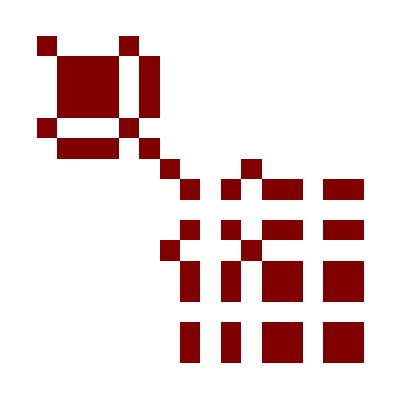

```mathematica
R`couplingRot//ArrayPlot
```

```mathematica
{R`σDiv}=R`nullVector.σsRot/.subst2//Simplify;
```

```mathematica
R`H.R`σDiv-R`σDiv.R`H//Simplify
```

(0 | 0 | -(2 nz px-2 ⅈ nz py+ⅈ nx λ+ny λ)/ϵ | -(2 (nx-ⅈ ny) (px-ⅈ py))/ϵ
0 | 0 | -(2 (nx+ⅈ ny) (px-ⅈ py))/ϵ | (2 nz px-2 ⅈ nz py-ⅈ nx λ-ny λ)/ϵ
(2 nz px+2 ⅈ nz py-ⅈ nx λ+ny λ)/ϵ | (2 (nx-ⅈ ny) (px+ⅈ py))/ϵ | 0 | 0
(2 (nx+ⅈ ny) (px+ⅈ py))/ϵ | (-2 nz (px+ⅈ py)+(-ⅈ nx+ny) λ)/ϵ | 0 | 0)

```mathematica
R`G.R`σDiv-R`σDiv.R`G//Simplify
```

((2 ⅈ (nx px+ny py) (nz-ϵ) λ)/ϵ | (λ (-2 nx^2 py+nx (2 ny (px+ⅈ py)+(nz-ϵ) λ)-ⅈ (2 ny^2 px+2 nz (px-ⅈ py) (nz-ϵ)+ny (nz-ϵ) λ)))/ϵ | (2 n^2 nz (px-ⅈ py)+2 nz (px-ⅈ py) (P^2-ϵ^2)+(ⅈ nx+ny) nz^2 λ+(ⅈ nx^3+nx^2 ny+ⅈ nx (ny^2+px^2-2 ⅈ px py-py^2-ϵ^2)+ny (ny^2-px^2+2 ⅈ px py+py^2-ϵ^2)) λ)/ϵ | (2 (nx-ⅈ ny) (px-ⅈ py) (n^2+P^2-ϵ^2))/ϵ
(λ (2 nx^2 py-ⅈ (2 ny^2 px+2 nz (px+ⅈ py) (nz-ϵ)+ny (nz-ϵ) λ)+nx (-2 ny px+2 ⅈ ny py-nz λ+ϵ λ)))/ϵ | -(2 ⅈ (nx px+ny py) (nz-ϵ) λ)/ϵ | (2 (nx+ⅈ ny) (px-ⅈ py) (n^2+P^2-ϵ^2))/ϵ | (-2 n^2 nz (px-ⅈ py)-2 nz (px-ⅈ py) (P^2-ϵ^2)+(ⅈ nx+ny) nz^2 λ+(ⅈ nx^3+nx^2 ny+ⅈ nx (ny^2+px^2-2 ⅈ px py-py^2-ϵ^2)+ny (ny^2-px^2+2 ⅈ px py+py^2-ϵ^2)) λ)/ϵ
(-2 n^2 nz (px+ⅈ py)+ⅈ (2 ⅈ nz (px+ⅈ py) (P^2-ϵ^2)+(nx+ⅈ ny) nz^2 λ+(nx^3+ⅈ nx^2 ny+nx (ny^2+px^2+2 ⅈ px py-py^2-ϵ^2)+ⅈ ny (ny^2-px^2-2 ⅈ px py+py^2-ϵ^2)) λ))/ϵ | -(2 (nx-ⅈ ny) (px+ⅈ py) (n^2+P^2-ϵ^2))/ϵ | -(2 ⅈ (nx px+ny py) (nz-ϵ) λ)/ϵ | (λ (2 nx^2 py-nx (2 ny (px+ⅈ py)+(-nz+ϵ) λ)+ⅈ (2 ny^2 px+2 nz (px-ⅈ py) (nz-ϵ)+ny (-nz+ϵ) λ)))/ϵ
-(2 (nx+ⅈ ny) (px+ⅈ py) (n^2+P^2-ϵ^2))/ϵ | (2 n^2 nz (px+ⅈ py)+ⅈ (2 nz (-ⅈ px+py) (P^2-ϵ^2)+(nx+ⅈ ny) nz^2 λ+(nx^3+ⅈ nx^2 ny+nx (ny^2+px^2+2 ⅈ px py-py^2-ϵ^2)+ⅈ ny (ny^2-px^2-2 ⅈ px py+py^2-ϵ^2)) λ))/ϵ | (λ (-2 nx^2 py+nx (2 ny (px-ⅈ py)+(-nz+ϵ) λ)+ⅈ (2 ny^2 px+2 nz (px+ⅈ py) (nz-ϵ)+ny (-nz+ϵ) λ)))/ϵ | (2 ⅈ (nx px+ny py) (nz-ϵ) λ)/ϵ)

```mathematica
R`σDiv  (*rat operator*)
```

((nz+ϵ)/ϵ | (nx-ⅈ ny)/ϵ | 0 | 0
(nx+ⅈ ny)/ϵ | 1-nz/ϵ | 0 | 0
0 | 0 | 1-nz/ϵ | -(nx-ⅈ ny)/ϵ
0 | 0 | -(nx+ⅈ ny)/ϵ | (nz+ϵ)/ϵ)

div responses

```mathematica
R`divResponsef=Table[R`VCoupling[R`σDiv,σsRot⟦j⟧]//Simplify,{j,1,16}] ;(*rat operator has response*)
```

```mathematica
R`divVResponse0=Table[R`VCoupling0[R`σDiv,σsRot⟦j⟧]//Simplify,{j,1,16}] ;
```

```mathematica
R`divVResponseCorr=Table[R`VCouplingCorr[R`σDiv,σsRot⟦j⟧]//Simplify,{j,1,16}] ;
R`divVResponse1=Table[R`VCoupling1[R`σDiv,σsRot⟦j⟧]//Simplify,{j,1,16}] ;
```

```mathematica
R`divResponse6Unrot=Table[R`VCoupling[R`σDivNorm,σs⟦j⟧]//Simplify,{j,1,6}] ;
```

```mathematica
R`divVZResponse/.(mx nx+my ny)->-mz nz//Simplify
```

{((my nx-mx ny) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(√(n^2-nz^2) ϵ (2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)),(mz (n^2-nz ϵ) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(√(n^2-nz^2) (nz-ϵ) ϵ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)),(mz (n^2-nz ϵ) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/((nz-ϵ)^2 ϵ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)),-(-2 mz nz (nz-ϵ) (-3 n^4-4 n^2 ϵ^2-ϵ^4+nz^2 λ^2+nz ϵ λ^2)+mz (n^2-nz^2) (2 n^4-2 ϵ^4-nz^2 λ^2+ϵ^2 λ^2))/(√(n^2-nz^2) (nz-ϵ) ϵ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)),(2 (my nx-mx ny) (3 n^4+4 n^2 ϵ^2+ϵ^4-nz^2 λ^2-nz ϵ λ^2))/(√(n^2-nz^2) ϵ (2 n^2+2 ϵ^2-nz λ-ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ)),(mz (2 n^6+4 ϵ^6+2 n^4 (2 nz^2-5 nz ϵ+2 ϵ^2)-nz^4 λ^2+nz^3 ϵ λ^2-ϵ^4 λ^2+2 nz^2 ϵ^2 (2 ϵ^2+λ^2)-nz ϵ^3 (6 ϵ^2+λ^2)+n^2 (-16 nz ϵ^3+nz^2 (8 ϵ^2-λ^2)+ϵ^2 (6 ϵ^2+λ^2))))/((nz-ϵ)^2 ϵ (-2 n^2-2 ϵ^2+nz λ+ϵ λ) (2 n^2+2 ϵ^2+nz λ+ϵ λ))}

```mathematica
R`divResponsef.R`couplingRotInversed/.subst2//Simplify
```

{0,0,0,(-mx nx-my ny)/(√(n^2-nz^2) ϵ),(my nx-mx ny)/(√(n^2-nz^2) ϵ),-mz/ϵ,0,0,0,0,0,0,0,0,0,0}

```mathematica
{(-mx nx-my ny)/(√(n^2-nz^2) ϵ),(my nx-mx ny)/(√(n^2-nz^2) ϵ),-mz/ϵ}.U3//Simplify
```

{-(mx (nx^2+ny^2))/((n^2-nz^2) ϵ),-(my (nx^2+ny^2))/((n^2-nz^2) ϵ),-mz/ϵ}

```mathematica
(*selfenergyCorrR[A_,B_]:=selfenergyCorrR[A,B]={}//PadRight[#,6]&;*)
```

```mathematica
(*selfenergyCorrA[A_,B_]:=selfenergyCorrA[A,B]={}//PadRight[#,6]&;*)
```

```mathematica
Inverse[IdentityMatrix[6]-R`couplingRot[[1;;6,1;;6]]]//Simplify
```

((2 (3 n^4+4 n^2 ϵ^2+ϵ^4-nz^2 λ^2-nz ϵ λ^2))/(9 n^4+6 n^2 ϵ^2+ϵ^4-4 nz^2 λ^2) | 0 | 0 | 0 | -((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(9 n^4+6 n^2 ϵ^2+ϵ^4-4 nz^2 λ^2) | 0
0 | (2 (2 n^6+3 nz^2 ϵ^4+ϵ^6+n^4 (nz^2-6 nz ϵ+3 ϵ^2)+nz^3 ϵ λ^2-nz ϵ^3 (2 ϵ^2+λ^2)+n^2 (-8 nz ϵ^3+nz^2 (4 ϵ^2-λ^2)+ϵ^2 (2 ϵ^2+λ^2))))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | -(√(n^2-nz^2) (nz-ϵ) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | ((nz-ϵ)^2 (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | 0 | -(√(n^2-nz^2) (nz-ϵ) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2)))
0 | -(√(n^2-nz^2) (nz-ϵ) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | (3 n^6-2 nz ϵ^5+ϵ^6+n^4 (6 nz^2-18 nz ϵ+7 ϵ^2)-2 nz^4 λ^2+6 nz^3 ϵ λ^2+2 nz^2 (ϵ^4-2 ϵ^2 λ^2)+n^2 (5 ϵ^4+nz^2 (8 ϵ^2-2 λ^2)+2 nz ϵ (-6 ϵ^2+λ^2)))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | (√(n^2-nz^2) (nz-ϵ) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | 0 | -((n^2-nz^2) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2)))
0 | ((nz-ϵ)^2 (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | (√(n^2-nz^2) (nz-ϵ) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | (2 (3 n^6+ϵ^6+n^4 ϵ (-6 nz+ϵ)+nz^4 λ^2-nz^3 ϵ λ^2+nz^2 ϵ^2 (2 ϵ^2+λ^2)-nz ϵ^3 (2 ϵ^2+λ^2)+n^2 (3 ϵ^4+nz^2 (6 ϵ^2-2 λ^2)+nz (-8 ϵ^3+2 ϵ λ^2))))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | 0 | (√(n^2-nz^2) (nz-ϵ) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2)))
-((n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(9 n^4+6 n^2 ϵ^2+ϵ^4-4 nz^2 λ^2) | 0 | 0 | 0 | (2 (3 n^4+4 n^2 ϵ^2+ϵ^4-nz^2 λ^2-nz ϵ λ^2))/(9 n^4+6 n^2 ϵ^2+ϵ^4-4 nz^2 λ^2) | 0
0 | -(√(n^2-nz^2) (nz-ϵ) (n^2 (nz-3 ϵ)+(3 nz-ϵ) ϵ^2) λ)/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | -((n^2-nz^2) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | (√(n^2-nz^2) (nz-ϵ) (3 n^4-2 n^2 ϵ^2-ϵ^4-2 nz^2 λ^2+2 nz ϵ λ^2))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))) | 0 | (3 n^6-2 nz ϵ^5+ϵ^6+n^4 (6 nz^2-18 nz ϵ+7 ϵ^2)-2 nz^4 λ^2+6 nz^3 ϵ λ^2+2 nz^2 (ϵ^4-2 ϵ^2 λ^2)+n^2 (5 ϵ^4+nz^2 (8 ϵ^2-2 λ^2)+2 nz ϵ (-6 ϵ^2+λ^2)))/(6 n^6+n^4 (3 nz^2-18 nz ϵ+5 ϵ^2)+ϵ (-2 nz ϵ^4+ϵ^5+4 nz^3 λ^2+nz^2 (3 ϵ^3-4 ϵ λ^2))+2 n^2 (2 ϵ^4+nz^2 (5 ϵ^2-2 λ^2)+nz (-6 ϵ^3+2 ϵ λ^2))))

```mathematica
({0,0,0,1,1,1}.%1395).R`divResponse//Simplify
```

(my (nx-ny)-mx (nx+ny)-mz √(n^2-nz^2))/(√(n^2-nz^2) ϵ)

```mathematica
R`couplingRotInversed.R`nullVectorᵀ//Simplify
```

(0
0
0
0
0
0
0
0
0
0
0
0
(√(n^2-nz^2))/ϵ
0
nz/ϵ
1)

## Total response

```mathematica
({{1-(2 (n^2+nz^2))/ϵ^2+(4 n^2 nz-2 nz (2 nz^2+λ^2))/ϵ^3, 0, -(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ}, {0, 1-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3, 0}, {-(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ, 0, (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2}})//turn3//Simplify//ben
```

((nx^2+ny^2)/(n^2-nz^2)-(2 (n^2 (nx^2+2 ny^2)+nx^2 nz^2))/((n^2-nz^2) ϵ^2)+(2 nz (-2 n^2 nx^2+ny^2 λ^2+nx^2 (2 nz^2+λ^2)))/((-n^2+nz^2) ϵ^3) | (4 nx ny nz)/ϵ^3+(2 nx ny)/ϵ^2 | -(nx (2 n^2+nz^2))/ϵ^3+(nx nz)/ϵ^2+nx/ϵ
(4 nx ny nz)/ϵ^3+(2 nx ny)/ϵ^2 | (nx^2+ny^2)/(n^2-nz^2)-(2 (n^2 (2 nx^2+ny^2)+ny^2 nz^2))/((n^2-nz^2) ϵ^2)+(2 nz (-2 n^2 ny^2+nx^2 λ^2+ny^2 (2 nz^2+λ^2)))/((-n^2+nz^2) ϵ^3) | -(ny (2 n^2+nz^2))/ϵ^3+(ny nz)/ϵ^2+ny/ϵ
-(nx (2 n^2+nz^2))/ϵ^3+(nx nz)/ϵ^2+nx/ϵ | -(ny (2 n^2+nz^2))/ϵ^3+(ny nz)/ϵ^2+ny/ϵ | (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2)

```mathematica
R`response0//ben
```

(1-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | 0 | 0 | 0 | -(3 n^2 λ)/ϵ^3-(3 nz λ)/ϵ^2+λ/ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | (2 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | ((n^2+2 nz^2) λ)/ϵ^3+(3 nz λ)/ϵ^2-λ/ϵ | 0 | (2 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (2 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2 | -(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ | 0 | (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((n^2+2 nz^2) λ)/ϵ^3+(3 nz λ)/ϵ^2-λ/ϵ | -(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ | 1-(2 (n^2+nz^2))/ϵ^2+(4 n^2 nz-2 nz (2 nz^2+λ^2))/ϵ^3 | 0 | -(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(3 n^2 λ)/ϵ^3-(3 nz λ)/ϵ^2+λ/ϵ | 0 | 0 | 0 | 1-(4 n^2)/ϵ^2-(2 nz λ^2)/ϵ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (2 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2 | -(√(n^2-nz^2) (2 n^2+nz^2))/ϵ^3+(nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ | 0 | (2 n^2 nz-2 nz^3)/ϵ^3+(n^2-nz^2)/ϵ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/6+(4 nz)/(9 ϵ)+(4 nz (-45 n^2+40 nz^2-3 λ^2))/(81 ϵ^3)+(-36 n^2+52 nz^2+3 λ^2)/(54 ϵ^2) | 0 | 0 | 0 | -1/6-(4 nz)/(9 ϵ)+(36 n^2-52 nz^2-3 λ^2)/(54 ϵ^2)+(4 nz (45 n^2-40 nz^2+3 λ^2))/(81 ϵ^3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3-(14 nz)/(9 ϵ)+(18 n^2+98 nz^2+15 λ^2)/(27 ϵ^2)-(nz (324 n^2+182 nz^2+255 λ^2))/(81 ϵ^3) | 0 | -1/3+(22 nz)/(9 ϵ)-(2 (9 n^2+41 nz^2+6 λ^2))/(27 ϵ^2)+(-180 n^2 nz+646 nz^3+231 nz λ^2)/(81 ϵ^3) | 0 | (3 nz √(n^2-nz^2))/ϵ^2-(√(n^2-nz^2))/ϵ-(√(n^2-nz^2) (4 n^2+11 nz^2+3 λ^2))/(3 ϵ^3) | (nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/(2 ϵ^2) | 0 | -(2 nz λ)/ϵ^2+λ/(2 ϵ)+(λ (4 n^2+17 nz^2+3 λ^2))/(6 ϵ^3) | ((n^2+3 nz^2) λ)/(2 ϵ^3)-(nz λ)/(2 ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3+(22 nz)/(9 ϵ)-(2 (9 n^2+41 nz^2+6 λ^2))/(27 ϵ^2)+(-180 n^2 nz+646 nz^3+231 nz λ^2)/(81 ϵ^3) | 0 | 2/3-(14 nz)/(9 ϵ)-(nz (36 n^2+470 nz^2+255 λ^2))/(81 ϵ^3)+(-2 n^2+5/27 (34 nz^2+3 λ^2))/ϵ^2 | 0 | -(3 nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ+(√(n^2-nz^2) (-4 n^2+19 nz^2+3 λ^2))/(3 ϵ^3) | -(nz √(n^2-nz^2) λ)/ϵ^3+(√(n^2-nz^2) λ)/(2 ϵ^2) | 0 | (2 nz λ)/ϵ^2-λ/(2 ϵ)-(λ (-4 n^2+25 nz^2+3 λ^2))/(6 ϵ^3) | -((n^2+3 nz^2) λ)/(2 ϵ^3)+(nz λ)/(2 ϵ^2)
0 | 0 | 0 | 0 | 0 | 0 | -1/6-(4 nz)/(9 ϵ)+(36 n^2-52 nz^2-3 λ^2)/(54 ϵ^2)+(4 nz (45 n^2-40 nz^2+3 λ^2))/(81 ϵ^3) | 0 | 0 | 0 | 1/6+(4 nz)/(9 ϵ)+(4 nz (-45 n^2+40 nz^2-3 λ^2))/(81 ϵ^3)+(-36 n^2+52 nz^2+3 λ^2)/(54 ϵ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 nz √(n^2-nz^2))/ϵ^2-(√(n^2-nz^2))/ϵ-(√(n^2-nz^2) (4 n^2+11 nz^2+3 λ^2))/(3 ϵ^3) | 0 | -(3 nz √(n^2-nz^2))/ϵ^2+(√(n^2-nz^2))/ϵ+(√(n^2-nz^2) (-4 n^2+19 nz^2+3 λ^2))/(3 ϵ^3) | 0 | (-4 n^2 nz+4 nz^3)/ϵ^3+(2 n^2-2 nz^2)/ϵ^2 | ((n^2-nz^2) λ)/ϵ^3 | 0 | (3 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | (nz √(n^2-nz^2) λ)/ϵ^3
0 | 0 | 0 | 0 | 0 | 0 | 0 | (nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/(2 ϵ^2) | 0 | -(nz √(n^2-nz^2) λ)/ϵ^3+(√(n^2-nz^2) λ)/(2 ϵ^2) | 0 | ((n^2-nz^2) λ)/ϵ^3 | (n^2-nz^2)/ϵ^2 | 0 | (nz √(n^2-nz^2))/ϵ^2-(√(n^2-nz^2) λ^2)/(2 ϵ^3) | -(n^2 √(n^2-nz^2))/ϵ^3+(√(n^2-nz^2))/ϵ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 nz λ)/ϵ^2+λ/(2 ϵ)+(λ (4 n^2+17 nz^2+3 λ^2))/(6 ϵ^3) | 0 | (2 nz λ)/ϵ^2-λ/(2 ϵ)-(λ (-4 n^2+25 nz^2+3 λ^2))/(6 ϵ^3) | 0 | (3 nz √(n^2-nz^2) λ)/ϵ^3-(√(n^2-nz^2) λ)/ϵ^2 | (nz √(n^2-nz^2))/ϵ^2-(√(n^2-nz^2) λ^2)/(2 ϵ^3) | 0 | -(2 nz λ^2)/ϵ^3+(nz^2+λ^2/2)/ϵ^2 | nz/ϵ-(nz (2 n^2+λ^2))/(2 ϵ^3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((n^2+3 nz^2) λ)/(2 ϵ^3)-(nz λ)/(2 ϵ^2) | 0 | -((n^2+3 nz^2) λ)/(2 ϵ^3)+(nz λ)/(2 ϵ^2) | 0 | (nz √(n^2-nz^2) λ)/ϵ^3 | -(n^2 √(n^2-nz^2))/ϵ^3+(√(n^2-nz^2))/ϵ | 0 | nz/ϵ-(nz (2 n^2+λ^2))/(2 ϵ^3) | 1-n^2/ϵ^2)

```mathematica
R`response0=R`couplingRotInversed.R`couplingRot//Simplify;
R`response1Dress=R`couplingRot.R`couplingRot//Simplify;
```

(1)
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
R`response1=R`couplingRotInversed[[1;;6,1;;6]].(R`VCouplingTable2//ben).R`couplingRotInversed[[7;;16,7;;16]]//Simplify;
```

```mathematica
R`responseK1=R`response0;
```

```mathematica
R`responseK2=R`responseK1//K2;
```

```mathematica
?K2
```

Global`K2

K2[A_]:=A/.{n→-n,nx→-nx,ny→-ny,nz→-nz,Λ→-Λ}

```mathematica
R`response=R`responseK1+R`responseK2;
R`responseMinus=R`responseK1-R`responseK2;
```

```mathematica
R`responseV=R`response1+(R`response1//K2);
R`responseVMinus=R`response1-(R`response1//K2);
```

```mathematica
R`responseUndressed=R`couplingRot+(R`couplingRot//K2);
```

```mathematica
R`responseUndressedMinus=R`couplingRot-(R`couplingRot//K2);
```

```mathematica
RU1`response=R`responseUndressed+R`response1Dress+(R`response1Dress//K2);
```

```mathematica
RU1`responseMinus=R`responseUndressedMinus+R`response1Dress-(R`response1Dress//K2);
```

## polarisations (minuses aren’t needed if we turn first using //turn3)

alphaMN

```mathematica
R`gdPM={{R`responseVMinus[[4,7]],R`responseVMinus[[4,8]],R`responseV[[4,9]]},{R`responseVMinus[[5,7]],R`responseVMinus[[5,8]],R`responseV[[5,9]]},{R`responseV[[6,7]],R`responseV[[6,8]],R`responseVMinus[[6,9]]}}//Simplify;
```

```mathematica
R`gdPMTurned=(R`gdPM//turn3)/.subst2//Simplify//ben
```

((2 ny (-my nx^2+mx nx ny+mz ny nz))/((n^2-nz^2) ϵ^2) | (2 ny (my nx ny-mx ny^2+mz nx nz))/((-n^2+nz^2) ϵ^2) | -(2 (3 ny (my nx-mx ny) nz+mz nx (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)
(2 nx (-my nx^2+mx nx ny+mz ny nz))/((-n^2+nz^2) ϵ^2) | -(2 (-my nx^2 ny+mx nx ny^2+mz nz (-n^2+ny^2+nz^2)))/((n^2-nz^2) ϵ^2) | -(2 (3 nx (-my nx+mx ny) nz+mz ny (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)
(4 mz nx)/ϵ^2 | (4 mz ny)/ϵ^2 | (6 mz nz)/ϵ^2)

```mathematica
(R`responseV[[4,9]]//Simplify)/.subst2//ben//Simplify
```

$Aborted

```mathematica
R`gdPM/.subst2//ben//Simplify
```

```mathematica
({{0, 0, -(2 mz (n^2+2 nz^2))/(√(n^2-nz^2) ϵ^2)}, {(2 (-my nx+mx ny))/ϵ^2, (2 mz nz)/ϵ^2, -(6 (my nx-mx ny) nz)/(√(n^2-nz^2) ϵ^2)}, {(4 mz √(n^2-nz^2))/ϵ^2, 0, (6 mz nz)/ϵ^2}})//turn3
```

((2 nx ny (-my nx+mx ny))/((n^2-nz^2) ϵ^2)+(2 mz ny^2 nz)/((n^2-nz^2) ϵ^2) | (2 ny^2 (-my nx+mx ny))/((n^2-nz^2) ϵ^2)-(2 mz nx ny nz)/((n^2-nz^2) ϵ^2) | -(6 ny (my nx-mx ny) nz)/((n^2-nz^2) ϵ^2)-(2 mz nx (n^2+2 nz^2))/((n^2-nz^2) ϵ^2)
-(2 nx^2 (-my nx+mx ny))/((n^2-nz^2) ϵ^2)-(2 mz nx ny nz)/((n^2-nz^2) ϵ^2) | -(2 nx ny (-my nx+mx ny))/((n^2-nz^2) ϵ^2)+(2 mz nx^2 nz)/((n^2-nz^2) ϵ^2) | (6 nx (my nx-mx ny) nz)/((n^2-nz^2) ϵ^2)-(2 mz ny (n^2+2 nz^2))/((n^2-nz^2) ϵ^2)
(4 mz nx)/ϵ^2 | (4 mz ny)/ϵ^2 | (6 mz nz)/ϵ^2)

```mathematica
(R`gdPMTurned/.subst2/.mx nx->-my ny - mz nz/.subst2ny//Simplify)/. (my ny+mz nz)->-mx nx//Simplify
```

(-(2 my ny (nx^2+ny^2))/((n^2-nz^2) ϵ^2) | (2 mx ny)/ϵ^2 | -(2 (3 ny (my nx-mx ny) nz+mz nx (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)
(2 my nx (nx^2+ny^2))/((n^2-nz^2) ϵ^2) | -(2 mx nx)/ϵ^2 | -(2 (3 nx (-my nx+mx ny) nz+mz ny (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)
(4 mz nx)/ϵ^2 | (4 mz ny)/ϵ^2 | (6 mz nz)/ϵ^2)

```mathematica
R`gdPMTurnedS=({{-(2 my ny)/ϵ^2, (2 mx ny)/ϵ^2, -(2 (3 ny (my nx-mx ny) nz+mz nx (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)}, {(2 my nx)/ϵ^2, -(2 mx nx)/ϵ^2, -(2 (3 nx (-my nx+mx ny) nz+mz ny (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)}, {(4 mz nx)/ϵ^2, (4 mz ny)/ϵ^2, (6 mz nz)/ϵ^2}});
```

```mathematica
(R`gdPMTurnedS-(4/ϵ^2 KroneckerProduct[m,nv2]-2/ϵ^2 KroneckerProduct[mpar,npar]+2/ϵ^2 KroneckerProduct[m,nper]-2/ϵ^2 KroneckerProduct[nv2,mper])//Simplify)/.msubst/.subst2//Simplify
```

((2 mz nz)/ϵ^2 | 0 | 0
0 | (2 mz nz)/ϵ^2 | 0
0 | 0 | (2 mz nz)/ϵ^2)

```mathematica
R`mnVector=nper×(m×ndot)-npar×(mpar×ndot)-mper×(nv2×ndot)+2 ndot mz nz//Simplify;
```

```mathematica
Simplify[((ϵ^2/2 R`gdPMTurnedS.ndot-R`mnVector)//Simplify),Assumptions->{my ny+mz nz+ mx nx ==0,nx^2+ny^2+nz^2==n^2,ndoty ny+ndotx nx+ndotz nz==0}]
```

{0,0,0}

alphaNM

```mathematica
R`gdNMTurnedS=({{-(2 my ny)/ϵ^2, (2 mx ny)/ϵ^2, -(2 (3 ny (my nx-mx ny) nz+mz nx (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)}, {(2 my nx)/ϵ^2, -(2 mx nx)/ϵ^2, -(2 (3 nx (-my nx+mx ny) nz+mz ny (n^2+2 nz^2)))/((n^2-nz^2) ϵ^2)}, {(4 mz nx)/ϵ^2, (4 mz ny)/ϵ^2, (6 mz nz)/ϵ^2}})//Transpose;
```

```mathematica
(R`gdNMTurnedS-(4/ϵ^2 KroneckerProduct[nv2,m]-2/ϵ^2 KroneckerProduct[npar,mpar]+2/ϵ^2 KroneckerProduct[nper,m]-2/ϵ^2 KroneckerProduct[mper,nv2])//Simplify)/.msubst/.subst2//Simplify
```

((2 mz nz)/ϵ^2 | 0 | 0
0 | (2 mz nz)/ϵ^2 | 0
0 | 0 | (2 mz nz)/ϵ^2)

```mathematica
R`nmVector=nper×(m×ndot)-npar×(mpar×ndot)-mper×(nv2×ndot)+2 ndot mz nz//Simplify;
```

s minus

```mathematica
{{(R`responseVMinus[[1,7]])/(R`response[[1,1]]),(R`responseVMinus[[2,7]])/(R`response[[2,2]])},{(R`responseVMinus[[1,8]])/(R`response[[1,1]]),(R`responseVMinus[[2,8]])/(R`response[[2,2]])},{(R`responseV[[1,9]])/(R`response[[1,1]]),(R`responseV[[2,9]])/(R`response[[2,2]])}}//Simplify//ben
```

(0 | (2 mz nz λ)/ϵ^3
-(2 mz nz λ)/ϵ^3 | 0
-(2 (my nx-mx ny) nz λ)/(√(n^2-nz^2) ϵ^3) | (mz (3 n^2-nz^2) λ)/(√(n^2-nz^2) ϵ^3))

```mathematica
R`sminus={{(R`responseV[[1,7]])/(R`response[[1,1]]),(R`responseV[[2,7]])/(R`response[[2,2]])},{(R`responseV[[1,8]])/(R`response[[1,1]]),(R`responseV[[2,8]])/(R`response[[2,2]])},{(R`responseVMinus[[1,9]])/(R`response[[1,1]]),(R`responseVMinus[[2,9]])/(R`response[[2,2]])}}//Simplify;
```

```mathematica
R`sminus//turn//ben
```

(0 | (mz (nx^2+ny^2) λ)/((n^2-nz^2) ϵ^2)
-(mz (nx^2+ny^2) λ)/((n^2-nz^2) ϵ^2) | 0
(ny (mx nx+my ny+mz nz) λ)/(2 (-n^2+nz^2) ϵ^2) | (nx (mx nx+my ny+mz nz) λ)/(2 (n^2-nz^2) ϵ^2))

```mathematica
R`sminus//turn//ben4
```

(-(4 mz nx ny λ)/ϵ^4 | (mz (nx^2+ny^2) λ)/((n^2-nz^2) ϵ^2)-(mz λ (-4 n^2 (9 nx^2+ny^2)+ny^2 (8 nz^2+λ^2)+nx^2 (40 nz^2+λ^2)))/(8 (n^2-nz^2) ϵ^4)
-(mz (nx^2+ny^2) λ)/((n^2-nz^2) ϵ^2)+(mz λ (-4 n^2 (nx^2+9 ny^2)+nx^2 (8 nz^2+λ^2)+ny^2 (40 nz^2+λ^2)))/(8 (n^2-nz^2) ϵ^4) | (4 mz nx ny λ)/ϵ^4
(ny (mx nx+my ny+mz nz) λ)/(2 (-n^2+nz^2) ϵ^2)-(λ (4 my n^2 (5 nx^2+6 ny^2)+6 my ny^2 λ^2+mz ny nz (236 n^2-200 nz^2+3 λ^2)+my nx^2 (-32 nz^2+3 λ^2)+mx nx ny (4 n^2+32 nz^2+3 λ^2)))/(24 (n^2-nz^2) ϵ^4) | (nx (mx nx+my ny+mz nz) λ)/(2 (n^2-nz^2) ϵ^2)+(λ (4 mx n^2 (6 nx^2+5 ny^2)+6 mx nx^2 λ^2+mz nx nz (236 n^2-200 nz^2+3 λ^2)+mx ny^2 (-32 nz^2+3 λ^2)+my nx ny (4 n^2+32 nz^2+3 λ^2)))/(24 (n^2-nz^2) ϵ^4))

```mathematica
R`sminusAntiSym6={{(R`responseVMinus[[1,7]])/(R`response[[1,1]]),(R`responseVMinus[[2,7]])/(R`response[[2,2]])},{(R`responseVMinus[[1,8]])/(R`response[[1,1]]),(R`responseVMinus[[2,8]])/(R`response[[2,2]])},{(R`responseV[[1,9]])/(R`response[[1,1]]),(R`responseV[[2,9]])/(R`response[[2,2]])}}//ben6//Simplify
```

(-((my nx-mx ny) (2 n^2-5 nz^2) λ)/(3 ϵ^5) | (6 (mx nx+my ny) λ^3+mz nz λ (-88 n^2+4 nz^2+48 ϵ^2+9 λ^2))/(24 ϵ^5)
-(mz nz λ (-32 n^2+12 nz^2+16 ϵ^2+λ^2))/(8 ϵ^5) | 0
-((my nx-mx ny) nz λ (-173 n^2+47 nz^2+36 ϵ^2-18 λ^2))/(18 √(n^2-nz^2) ϵ^5) | (126 (mx nx+my ny) nz λ^3+mz λ (276 n^4-nz^2 (164 nz^2+72 ϵ^2+117 λ^2)+n^2 (-616 nz^2+216 ϵ^2+171 λ^2)))/(72 √(n^2-nz^2) ϵ^5))

```mathematica
R`sminusAntiSym={{(R`responseVMinus[[1,7]])/(R`response[[1,1]]),(R`responseVMinus[[2,7]])/(R`response[[2,2]])},{(R`responseVMinus[[1,8]])/(R`response[[1,1]]),(R`responseVMinus[[2,8]])/(R`response[[2,2]])},{(R`responseV[[1,9]])/(R`response[[1,1]]),(R`responseV[[2,9]])/(R`response[[2,2]])}}//ben//Simplify
```

(0 | (2 mz nz λ)/ϵ^3
-(2 mz nz λ)/ϵ^3 | 0
(2 (-my nx+mx ny) nz λ)/(√(n^2-nz^2) ϵ^3) | (mz (3 n^2-nz^2) λ)/(√(n^2-nz^2) ϵ^3))

```mathematica
R`sminusAntiSym6//turn//#/.subst2&//Simplify
```

((nx λ (mx nx ny (8 n^2-20 nz^2+3 λ^2)+mz ny nz (4 n^2-16 nz^2+3 λ^2)+my (-8 n^2 nx^2+20 nx^2 nz^2+3 ny^2 λ^2)))/(12 (n^2-nz^2) ϵ^5) | (λ (2 my ny (20 nx^2 nz^2+3 (ny^2+nz^2) λ^2-n^2 (8 nx^2+3 λ^2))+2 mx nx (3 nz^2 λ^2+n^2 (8 ny^2-3 λ^2)+ny^2 (-20 nz^2+3 λ^2))+mz nz (88 n^4+n^2 (8 ny^2-92 nz^2-48 ϵ^2-9 λ^2)+ny^2 (-32 nz^2+6 λ^2)+nz^2 (4 nz^2+48 ϵ^2+9 λ^2))))/(24 (n^2-nz^2) ϵ^5)
(λ (2 mx nx ny^2 (8 n^2-20 nz^2+3 λ^2)+my (-16 n^2 nx^2 ny+40 nx^2 ny nz^2+6 ny^3 λ^2)+mz nz (-8 n^2 (12 nx^2+11 ny^2)+3 nx^2 (12 nz^2+16 ϵ^2+λ^2)+ny^2 (4 nz^2+48 ϵ^2+9 λ^2))))/(24 (n^2-nz^2) ϵ^5) | -(ny λ (my nx ny (8 n^2-20 nz^2+3 λ^2)+mz nx nz (4 n^2-16 nz^2+3 λ^2)+mx (-8 n^2 ny^2+20 ny^2 nz^2+3 nx^2 λ^2)))/(12 (n^2-nz^2) ϵ^5)
(126 ny (mx nx+my ny) nz λ^3-4 nx (my nx-mx ny) nz λ (-173 n^2+47 nz^2+36 ϵ^2-18 λ^2)+mz ny λ (276 n^4-nz^2 (164 nz^2+72 ϵ^2+117 λ^2)+n^2 (-616 nz^2+216 ϵ^2+171 λ^2)))/(72 (n^2-nz^2) ϵ^5) | (4 ny (-my nx+mx ny) nz λ (-173 n^2+47 nz^2+36 ϵ^2-18 λ^2)-nx (126 (mx nx+my ny) nz λ^3+mz λ (276 n^4-nz^2 (164 nz^2+72 ϵ^2+117 λ^2)+n^2 (-616 nz^2+216 ϵ^2+171 λ^2))))/(72 (n^2-nz^2) ϵ^5))

```mathematica
R`sminusAntiSymTurn=(R`sminusAntiSym//turn)/.subst2//Simplify
```

(0 | -(2 mz nz λ)/ϵ^3
(2 mz nz λ)/ϵ^3 | 0
((2 nx (-my nx+mx ny) nz+mz ny (3 n^2-nz^2)) λ)/((n^2-nz^2) ϵ^3) | ((2 ny (-my nx+mx ny) nz+mz nx (-3 n^2+nz^2)) λ)/((n^2-nz^2) ϵ^3))

```mathematica
R`conductivity={R`response[[1,1]],R`response[[2,2]]}/.λ->0//Simplify
R`conductivityUndressed={R`responseUndressed[[1,1]],R`responseUndressed[[2,2]]};
```

{-(2 (n^2-ϵ^2))/(3 n^2+ϵ^2),-(2 (n^2-ϵ^2))/(3 n^2+ϵ^2)}

```mathematica
R`splusElectric={{R`response[[1,4]],R`response[[2,4]]},{R`response[[1,5]],R`response[[2,5]]},{R`responseMinus[[1,6]],R`responseMinus[[2,6]]}}//Simplify;
```

```mathematica
R`splus={{(R`response[[1,4]])/(R`response[[1,1]]),(R`response[[2,4]])/(R`response[[2,2]])},{(R`response[[1,5]])/(R`response[[1,1]]),(R`response[[2,5]])/(R`response[[2,2]])},{(R`responseMinus[[1,6]])/(R`response[[1,1]]),(R`responseMinus[[2,6]])/(R`response[[2,2]])}}//Simplify;
```

```mathematica
R`splusUndressed={{(R`responseUndressed[[1,4]])/(R`responseUndressed[[1,1]]),(R`responseUndressed[[2,4]])/(R`responseUndressed[[2,2]])},{(R`responseUndressed[[1,5]])/(R`responseUndressed[[1,1]]),(R`responseUndressed[[2,5]])/(R`responseUndressed[[2,2]])},{(R`responseUndressedMinus[[1,6]])/(R`responseUndressed[[1,1]]),(R`responseUndressedMinus[[2,6]])/(R`responseUndressed[[2,2]])}}//Simplify;
```

```mathematica
R`sminusElectric={{R`responseMinus[[1,13]],R`responseMinus[[2,13]]},{R`responseMinus[[1,14]],R`responseMinus[[2,14]]},{R`response[[1,15]],R`response[[2,15]]}}//Simplify;
```

```mathematica
R`gd={{R`response[[13,13]],R`response[[13,14]],R`responseMinus[[13,15]]},{R`response[[14,13]],R`response[[14,14]],R`responseMinus[[14,15]]},{R`responseMinus[[15,13]],R`responseMinus[[15,14]],R`response[[15,15]]}}/.subst2//Simplify;
```

```mathematica
R`gdUndressed={{R`responseUndressed[[13,13]],R`responseUndressed[[13,14]],R`responseUndressedMinus[[13,15]]},{R`responseUndressed[[14,13]],R`responseUndressed[[14,14]],R`responseUndressedMinus[[14,15]]},{R`responseUndressedMinus[[15,13]],R`responseUndressedMinus[[15,14]],R`responseUndressed[[15,15]]}}/.subst2//Simplify;
```

```mathematica
R`gdPlus={{R`response[[4,4]],R`response[[4,5]],R`responseMinus[[4,6]]},{R`response[[5,4]],R`response[[5,5]],R`responseMinus[[5,6]]},{R`responseMinus[[6,4]],R`responseMinus[[6,5]],R`response[[6,6]]}}/.subst2//Simplify;
```

```mathematica
R`gdPlusUndressed={{R`responseUndressed[[4,4]],R`responseUndressed[[4,5]],R`responseUndressedMinus[[4,6]]},{R`responseUndressed[[5,4]],R`responseUndressed[[5,5]],R`responseUndressedMinus[[5,6]]},{R`responseUndressedMinus[[6,4]],R`responseUndressedMinus[[6,5]],R`responseUndressed[[6,6]]}}/.subst2//Simplify;
```

```mathematica
RU1`conductivity={RU1`response[[1,1]],RU1`response[[2,2]]};
RU1`splus={{(RU1`response[[1,4]])/(RU1`response[[1,1]]),(RU1`response[[2,4]])/(RU1`response[[2,2]])},{(RU1`response[[1,5]])/(RU1`response[[1,1]]),(RU1`response[[2,5]])/(RU1`response[[2,2]])},{(RU1`responseMinus[[1,6]])/(RU1`response[[1,1]]),(RU1`responseMinus[[2,6]])/(RU1`response[[2,2]])}}//Simplify;RU1`gd={{RU1`response[[13,13]],RU1`response[[13,14]],RU1`responseMinus[[13,15]]},{RU1`response[[14,13]],RU1`response[[14,14]],RU1`responseMinus[[14,15]]},{RU1`responseMinus[[15,13]],RU1`responseMinus[[15,14]],RU1`response[[15,15]]}}/.subst2//Simplify;
RU1`gdPlus={{RU1`response[[4,4]],RU1`response[[4,5]],RU1`responseMinus[[4,6]]},{RU1`response[[5,4]],RU1`response[[5,5]],RU1`responseMinus[[5,6]]},{RU1`responseMinus[[6,4]],RU1`responseMinus[[6,5]],RU1`response[[6,6]]}}/.subst2//Simplify;
```

## Turning

```mathematica
U={{nx,ny},{ny,-nx}}/√(n^2-nz^2);turn={(U.#[[1;;2,1;;2]].U)[[1,All]],(U.#[[1;;2,1;;2]].U)[[2,All]],#[[3,1;;2]].U}&;
```

```mathematica
DumpSave["Rashba.mx","R`"];
DumpSave["Global.mx","Global`"];
DumpSave["RashbaUndressed.mx","RU`"];
DumpSave["Rashba1dress.mx","RU1`"]
```

{RU1`}

```mathematica
End[];
```

# Какие-то разложения

```mathematica
ss[A_]:=Series[(A/.{λ->γ n,nz->n nz,nx->n nx,ny->n ny})//Simplify,{γ,0,3}]//Simplify//Normal
bs[A_]:=Series[(A/.{nz->n nz,nx->n nx,ny->n ny}/.n->η λ)//Simplify,{η,0,3}]//Simplify//Normal
ben[A_]:=Series[A,{ϵ,∞,3}]//Simplify//Normal
ben4[A_]:=Series[A,{ϵ,∞,4}]//Simplify//Normal
ben6[A_]:=Series[A,{ϵ,∞,6}]//Simplify//Normal
```

```mathematica
R`gdPM
```

(-(-8 (-mx nx-my ny) nz+mz (-18 n^2+6 nz^2-4 nz ϵ+4 ϵ^2-λ^2))/(4 ϵ^3)+(8 (mx nx+my ny) nz+mz (-18 n^2+6 nz^2+4 nz ϵ+4 ϵ^2-λ^2))/(4 ϵ^3) | 0 | (-4 mz (n^2-nz^2) (2 nz-ϵ)+mx nx (6 n^2+14 nz^2-4 nz ϵ-4 ϵ^2-λ^2)+my ny (6 n^2+14 nz^2-4 nz ϵ-4 ϵ^2-λ^2))/(4 √(n^2-nz^2) ϵ^3)+(-4 mz (n^2-nz^2) (-2 nz-ϵ)-mx nx (6 n^2+14 nz^2+4 nz ϵ-4 ϵ^2-λ^2)-my ny (6 n^2+14 nz^2+4 nz ϵ-4 ϵ^2-λ^2))/(4 √(n^2-nz^2) ϵ^3)
0 | -(mz (-16 n^2+4 nz^2-4 nz ϵ+4 ϵ^2-λ^2))/(4 ϵ^3)+(mz (-16 n^2+4 nz^2+4 nz ϵ+4 ϵ^2-λ^2))/(4 ϵ^3) | -((my nx-mx ny) (16 n^2+4 nz^2-4 nz ϵ-4 ϵ^2-λ^2))/(4 √(n^2-nz^2) ϵ^3)-((-my nx+mx ny) (16 n^2+4 nz^2+4 nz ϵ-4 ϵ^2-λ^2))/(4 √(n^2-nz^2) ϵ^3)
(mz √(n^2-nz^2) (-4 nz+ϵ))/ϵ^3+(mz √(n^2-nz^2) (4 nz+ϵ))/ϵ^3 | 0 | (-4 (mx nx+my ny) nz+mz (12 n^2-4 nz^2-4 nz ϵ-4 ϵ^2-λ^2))/(4 ϵ^3)-(4 (-mx nx-my ny) nz+mz (12 n^2-4 nz^2+4 nz ϵ-4 ϵ^2-λ^2))/(4 ϵ^3))